```mathematica
Needs["PlotLegends`"]
kelvin[celsius_]:=273.15+celsius
celsius[kelvin_]:=kelvin-273.15
```

```mathematica
Mathematica plot formats
```

formats Mathematica plot

```mathematica
ticklist={{12,1},{24,2},{36,3},{48,4},{60,5},{72,6},{84,7},{96,8},{108,9},{120,10},{132,11},{144,12},{156,13},{168,14}};
axesstyle={Directive[18,Bold],Directive[18,Bold]};
plotstyle={Green,Thickness[0.005]};
plotformat={Ticks->{ticklist,Automatic},AxesStyle->axesstyle,PlotStyle-> plotstyle,ImageSize->600};
```

```mathematica
Step size for calculation
in years,total 14 y
```

calculation for size Step

```mathematica
step=1/12;
nyears =14;
nstep = nyears/step;
```

1. Safety factors
Safety factor on layout (number of channels,layers etc.)

```mathematica
safetylayout=0.0;
```

safety factor on fluence (calculations, machine predictions etc.)

```mathematica
safetyfluence=0.5;
```

Safety factor on thermal impedance of local support

```mathematica
safetythermalimpedance=0.2;
```

Safety factor on electrical power estimates

```mathematica
safetycurrent=0.2;
```

Scale factor for bias voltage (default is 500V)

```mathematica
vbiasscale=1.;
```

Coolant temperature
Coolant temperature in Celsius in each year for 14 y of operation

```mathematica
coolantT={{-35, -35, -35, -35, -35, -35, -35, -35, -35, -35, -35, -35, -35, -35}};
(*coolantT={{-25, -25, -25, -25, -25, -25, -25, -25, -25, -25, -25, -25, -25, -25}};*)
(*coolantT={{0, -5, -10, -15, -15, -20, -20, -25, -30, -35, -35, -35, -35, -35}};*)
(*coolantT={{0, -5, -10, -15, -15, -20, -20, -25, -25, -25, -25, -25, -25, -25}};*)
```

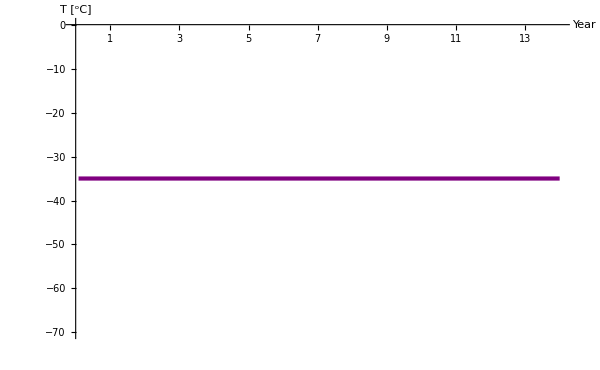

```mathematica
tc=List[];
For[i=0,i<nyears,i=i+step,
tc=Append[tc,Flatten[coolantT][[IntegerPart[i+1]]]];
]
Tcoolantplot=ListLinePlot[tc,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Purple,Thickness[0.005]},plotformat]
```

2.Layout
number of staves per end

```mathematica
nstavesb1=28;
nstavesb2=40;
nstavesb3=56;
nstavesb4=72;
```

number of modules per stave per side

```mathematica
nmod=14;
```

3. Powering efficiency
Feast efficiency

```mathematica
Clear[i]
feasteffdata={{0.5,60,66.2},{1,60,73},{1.5,60,75.1},{2,60,74.3},{2.5,60,71.1},{3,60,67.8},{4,60,63},{0.5,10,67.9},{1,10,75.1},{1.5,10,77.6},{2,10,77.3},{2.5,10,75.5},{3,10,72.1},{4,10,65}};
Text[Row[{"Data (I_load[A], T_sensor[degC], efficiency): ",TraditionalForm[feasteffdata]}]]
feasteff1[x1_,x2_,x3_,x4_,iload_,tsensor_]:=x1+x2*iload+x3*iload^2+x4*iload^3-2/25*tsensor
feastfit=FindFit[feasteffdata,feasteff1[a,b,c,d,il,t],{a,b,c,d},{il,t}];
feastfitconstants={a,b,c,d}/.feastfit;
feasteff[tsensor_,iload_]:=feastfitconstants[[1]]+feastfitconstants[[2]]*iload+feastfitconstants[[3]]*iload^2+feastfitconstants[[4]]*iload^3-2/25*tsensor
animation = Table[Show[Plot3D[feasteff[y,x],{x,0,4},{y,9,61},PlotRange->{{0,4},{9,61},{60,80}},ViewPoint->{2,1.5-1.2*Sin[2*Pi*(i/30-1)],0.3},ImageSize->600,AxesEdge->{{1,-1},{1,-1},{-1,1}},AxesStyle->{Directive[18,Bold],Directive[18,Bold],Directive[18,Bold]}],ListPointPlot3D[feasteffdata,PlotStyle->PointSize[0.02]],AxesLabel->{"I_load[A]","T [^oC]","Efficiency [%]"}],{i,0,30}];
animation[[1]]
SetDirectory[NotebookDirectory[]];
Export["FEAST eff.gif",animation,"GIF","DisplayDurations"->0.2];
Text[Row[{"Fit function used: ",TraditionalForm[feasteff1[a,b,c,d,Subscript[i, load],T]],", with the coefficients: a=",TraditionalForm[feastfitconstants[[1]]],", b=",TraditionalForm[feastfitconstants[[2]]], ", c=",TraditionalForm[feastfitconstants[[3]]], ", d=",TraditionalForm[feastfitconstants[[4]]]}]]
```

Data (I_load[A], T_sensor[degC], efficiency): (0.5 | 60 | 66.2
1 | 60 | 73
1.5 | 60 | 75.1
2 | 60 | 74.3
2.5 | 60 | 71.1
3 | 60 | 67.8
4 | 60 | 63
0.5 | 10 | 67.9
1 | 10 | 75.1
1.5 | 10 | 77.6
2 | 10 | 77.3
2.5 | 10 | 75.5
3 | 10 | 72.1
4 | 10 | 65)

-Graphics3D-

Fit function used: a+b i_load+c i_load^2+d i_load^3-(2 T)/25, with the coefficients: a=58.0448, b=29.6715, c=-12.4747, d=1.40142

```mathematica
Vfeast=10.5;(*Feast input voltage*)
```

DCDC2 efficiency

```mathematica
DCDC2eff=0.88;
```

4. Cable losses
loss factors in cables: on the stave (in tapes), in type 1 (service modules), and outer cables (PP1 to USA15)
From Tony:

```mathematica
losstype1=0.05;
lossouter=0.05;
```

4. Front-end components (before irradiation)
This section includes the ABC and Hybrid Controller Chips analogue and digital parts. These chips are fabricated in Global Foundries (formerly IBM) 130nm process that is known to suffer from an increase in the digital current due to ionizing radiation.

```mathematica
hybridV=1.5;
```

HCC digital

```mathematica
hccId=0.125*(1+safetycurrent);
```

HCC analog

```mathematica
hccIa=0.075*(1+safetycurrent);
```

ABC digital

```mathematica
abcId=0.035*(1+safetycurrent);
```

ABC analog

```mathematica
abcIa=0.066*(1+safetycurrent);
```

AMACII chip

```mathematica
amac15V=1.5;amac15I=0.045*(1+safetycurrent);amac15eff=0.65;
amac3V=3.0;amac3I=0.002*(1+safetycurrent);amac3eff=0.65;
```

5. EOS components (before irradiation)
There is one EOS card per stave (petal) side, two per stave/petal. Note that these components are not in IBM technology and will not suffer the current bump.

```mathematica
eosV12=1.2;eosV25=2.5;
```

lpGBTx

```mathematica
lpgbtI=0.625*(1+safetycurrent);
```

GBTIA

```mathematica
gbtiaI=0.053*(1+safetycurrent);
```

GBLD10
includes power for opto-converter

```mathematica
gbld25I=0.018*(1+safetycurrent);
gbld12I=0.0095*(1+safetycurrent);
```

6. Increase in digital current in ABC
TID Peak
Fit based on data presented by Richard Teuscher at the ITk week in Valencia

```mathematica
(*data={{-25,2.3,2.5},{-10,2.3,1.9},{-10,0.6,1.3},{-25,1250,9.7},{-15,62,3.9},{-15,2250,13.6},{20,2250,5.2},{-10,0.6,1.56},{-10,1.1,1.86},{-10,2.5,2.56}};*)data={{-25,2.3,2.5},{-10,2.3,1.9},{-10,0.6,1.3},{-15,62,3.9},{-10,0.6,1.56},{-10,1.1,1.86},{-10,2.5,2.56}};
Text[Row[{"Data (T [^0C], d [kRad/hr], factor): ",TraditionalForm[data]}]]
```

Data (T [^0C], d [kRad/hr], factor): (-25 | 2.3 | 2.5
-10 | 2.3 | 1.9
-10 | 0.6 | 1.3
-15 | 62 | 3.9
-10 | 0.6 | 1.56
-10 | 1.1 | 1.86
-10 | 2.5 | 2.56)

```mathematica
tidscale[x_,y_,z_,doserate_,T_]:=1+x*doserate^z*Exp[y*(20-T)]
fit=FindFit[data,tidscale[a,b,c,d,T],{{a,0.4},{b,0.02},{c,0.33}},{T,d}];
fitconstants={a,b,c}/.fit;
tidscalec1=fitconstants[[1]];
tidscalec2=fitconstants[[2]];
tidscalec3=fitconstants[[3]];Text[Row[{"Fit function used: ",TraditionalForm[tidscale[a,b,c,d,T]],", with the coefficients: a=",TraditionalForm[tidscalec1],", b=",TraditionalForm[tidscalec2], ", c=",TraditionalForm[tidscalec3]}]]
(*Show[Plot3D[tidscale[tidscalec1,tidscalec2,tidscalec3,d,T],{T,-25,20},{d,0,2500}],ListPointPlot3D[data,PlotStyle->PointSize[0.02]],AxesLabel->{"T [^oC]","Dose rate [kRad/h]","scale factor"}]*)
animation = Table[Show[Plot3D[tidscale[tidscalec1,tidscalec2,tidscalec3,d,T],{T,-25,20},{d,0,2500},ViewPoint->{2,-1.5+1.2*Sin[2*Pi*(i/30-1)],-1.2*Cos[Pi*(i/30-1)]},ImageSize->600,AxesEdge->{{-1,-1},{1,-1},{1,1}},AxesStyle->{Directive[18,Bold],Directive[18,Bold],Directive[18,Bold]}],ListPointPlot3D[data,PlotStyle->PointSize[0.02]],AxesLabel->{"T [^oC]","Dose rate [kRad/h]","scale factor"}],{i,0,30}];
animation[[1]]
SetDirectory[NotebookDirectory[]];
Export["TID scale.gif",animation,"GIF","DisplayDurations"->0.5,"TransitionEffect"->Background];
animation = Table[Show[Plot3D[tidscale[tidscalec1,tidscalec2,tidscalec3,d,T],{T,-25,20},{d,0,3},ViewPoint->{-2,-1.5+1.2*Sin[2*Pi*(i/30-1)],-1.2*Cos[Pi*(i/30-1)]},ImageSize->600,AxesEdge->{{-1,-1},{-1,-1},{1,-1}},AxesStyle->{Directive[18,Bold],Directive[18,Bold],Directive[18,Bold]}],ListPointPlot3D[data,PlotStyle->PointSize[0.02]],AxesLabel->{"T [^oC]","Dose rate [kRad/h]","scale factor"}],{i,0,30}];
animation[[1]]
Export["TID scale 2.gif",animation,"GIF","DisplayDurations"->0.5,"TransitionEffect"->Background];
```

Fit function used: a ⅇ^(b (20-T)) d^c+1, with the coefficients: a=0.38201, b=0.0245617, c=0.287121

-Graphics3D-

-Graphics3D-

Scale factor for the current at a specific collected dose
Parametrization by Graham Beck

```mathematica
coeff1=1.8;coeff2=0.4;norm=(1-Exp[-coeff1*(Log[coeff2/coeff1]/(coeff2-coeff1))])-(1-Exp[-coeff2*(Log[coeff2/coeff1]/(coeff2-coeff1))]);
scaleI[collecteddose_]:=Max[(1-Exp[-coeff1*(collecteddose-400)/1000])-(1-Exp[-coeff2*(collecteddose-400)/1000]),0]/norm
```

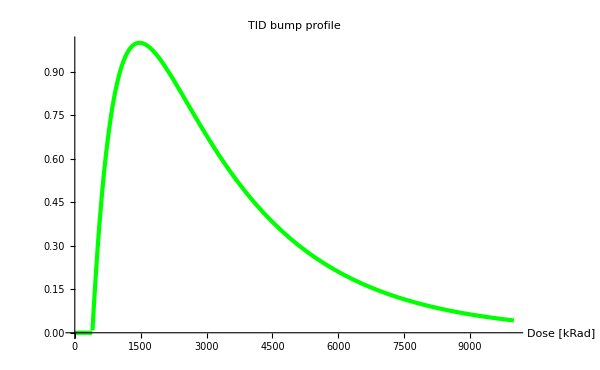

```mathematica
Plot[scaleI[d],{d,0,10000},PlotStyle-> plotstyle,PlotLabel->Style["TID bump profile",Bold,24],AxesLabel->{"Dose [kRad]",None},AxesStyle->axesstyle,ImageSize->600]
```

Combined scalefactor for digital ABC current

```mathematica
scale[T_,doserate_,collecteddose_]:=1+(tidscale[tidscalec1,tidscalec2,tidscalec3,doserate,T]-1)*scaleI[collecteddose]
```

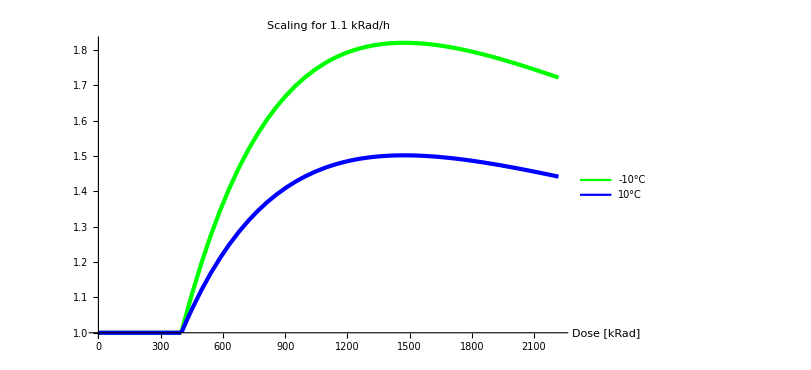

```mathematica
plot1=Plot[scale[-10,1.1,d],{d,0,2218},PlotStyle-> plotstyle,PlotLabel->Style["TID bump profile",Bold,24],AxesLabel->{"Dose [kRad]",None},AxesStyle->axesstyle,ImageSize->600];
plot2=Plot[scale[10,1.1,d],{d,0,2218},PlotLabel->Style["TID bump profile",Bold,24],AxesLabel->{"Dose [kRad]",None},AxesStyle->axesstyle,ImageSize->600,PlotStyle->{Blue,Thickness[0.005]}];
Legended[Show[plot1,plot2,PlotLabel->Style["Scaling for 1.1 kRad/h",Bold,24],LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue},{ Style["-10°C",16,Bold],Style["10°C",16,Bold]},LegendFunction->Framed],{{0.9,0.4},{1,1}}]]
```

7. Sensor Properties

Sensor area in cm2

```mathematica
area=9.554*9.554
```

91.2789

Bias voltage (incl. resistors)

```mathematica
vbias=500*vbiasscale;(*bias voltage is 500V*)
Rhv=10000;(*HV resistors are 2 times 5k*)
Rhvmux=1000000;(*parallel resistor for MUX operation is 1M*)
```

8. Nominal power

```mathematica
nomsensorT=0;
```

Module power (including powering efficiency)
General parameters

```mathematica
(*Vmod=10.5;(*input voltage to FEAST is 10.5 V*)*)
Rtape=0.01;(*tape resistance is 0.01 Ohm per module worst case*)
Pamac=(amac15V*amac15I+amac3V*amac3I)*(1+safetycurrent);
(*Pfamac=amac15V*amac15I*(1/amac15eff-1)+amac3V*amac3I*(1/amac3eff-1); old *)
Pfamac= (Vfeast-amac15V)*amac15I+(Vfeast-amac3V)*amac3I;(*Power in the FEAST chip due to AMAC supply*)
Prhv[Is_]:=Rhv*Is^2
Phvmux=vbias^2/(Rhvmux+Rhv);
Phv[Is_]:=Phvmux+Prhv[Is]
```

```mathematica
Short strip module
```

module Short strip

```mathematica
ssIabc[Tabc_,d_,D_]:=20*(scale[Tabc,d,D]*abcId+abcIa)
ssPabc[Tabc_,d_,D_]:=hybridV*ssIabc[Tabc,d,D]
ssIhcc[Thcc_,d_,D_]:=2*(scale[Thcc,d,D]*hccId+hccIa)
ssPhcc[Thcc_,d_,D_]:=hybridV*ssIhcc[Thcc,d,D]
ssIfeast[Tabc_,Thcc_,d_,D_]:=ssIabc[Tabc,d,D]+ssIhcc[Thcc,d,D]
ssPfeast[Tabc_,Thcc_,Tfeast_,d_,D_]:=Pfamac+(ssPabc[Tabc,d,D]+ssPhcc[Thcc,d,D])*(100/feasteff[Tfeast,ssIfeast[Tabc,Thcc,d,D]]-1)
ssIdig[Tabc_,Thcc_,d_,D_]:=(20*scale[Tabc,d,D]*abcId+2*scale[Thcc,d,D]*hccId)
ssItape[Tabc_,Thcc_,Tfeast_,d_,D_]:=(ssPabc[Tabc,d,D]+ssPhcc[Thcc,d,D]+Pamac+ssPfeast[Tabc,Thcc,Tfeast,d,D])/Vfeast
ssPtape[Tabc_,Thcc_,Tfeast_,d_,D_]:=(nmod*ssItape[Tabc,Thcc,Tfeast,d,D])^2*Rtape
ssPmod[Tabc_,Thcc_,Tfeast_,d_,D_,Is_]:=ssPabc[Tabc,d,D]+ssPhcc[Thcc,d,D]+Pamac+ssPfeast[Tabc,Thcc,Tfeast,d,D]+ssPtape[Tabc,Thcc,Tfeast,d,D]+Phv[Is]
ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0]
ssIfeast[nomsensorT,nomsensorT,1,0]
feasteff[nomsensorT,ssIfeast[nomsensorT,nomsensorT,1,0]]
```

7.56038

2.904

73.3299

Long strip module

```mathematica
lsIabc[Tabc_,d_,D_]:=10*(scale[Tabc,d,D]*abcId+abcIa)
lsPabc[Tabc_,d_,D_]:=hybridV*lsIabc[Tabc,d,D]
lsIhcc[Thcc_,d_,D_]:=scale[Thcc,d,D]*hccId+hccIa
lsPhcc[Thcc_,d_,D_]:=hybridV*lsIhcc[Thcc,d,D]
lsIfeast[Tabc_,Thcc_,d_,D_]:=lsIabc[Tabc,d,D]+lsIhcc[Thcc,d,D]
lsPfeast[Tabc_,Thcc_,Tfeast_,d_,D_]:=Pfamac+(lsPabc[Tabc,d,D]+lsPhcc[Thcc,d,D])*(100/feasteff[Tfeast,lsIfeast[Tabc,Thcc,d,D]]-1)
lsIdig[Tabc_,Thcc_,d_,D_]:=(10*scale[Tabc,d,D]*abcId+scale[Thcc,d,D]*hccId)
lsItape[Tabc_,Thcc_,Tfeast_,d_,D_]:=(lsPabc[Tabc,d,D]+lsPhcc[Thcc,d,D]+Pamac+lsPfeast[Tabc,Thcc,Tfeast,d,D])/Vfeast
lsPtape[Tabc_,Thcc_,Tfeast_,d_,D_]:=(nmod*lsItape[Tabc,Thcc,Tfeast,d,D])^2*Rtape
lsPmod[Tabc_,Thcc_,Tfeast_,d_,D_,Is_]:=lsPabc[Tabc,d,D]+lsPhcc[Thcc,d,D]+Pamac+lsPfeast[Tabc,Thcc,Tfeast,d,D]+lsPtape[Tabc,Thcc,Tfeast,d,D]+Phv[Is]
lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0]
```

3.81126

EOS power (including powering efficiency)
Short strip EOS

```mathematica
sseosI=(2*lpgbtI+2*gbld12I)/DCDC2eff*eosV12/eosV25+gbtiaI+2*gbld25I;
sseosP[Teos_]:=eosV25*sseosI*100/feasteff[Teos,sseosI]
sseosP[nomsensorT]
```

3.08152

```mathematica
Long strip EOS
```

EOS Long strip

```mathematica
lseosI=(lpgbtI+gbld12I)/DCDC2eff*eosV12/eosV25+gbtiaI+gbld25I;
lseosP[Teos_]:=eosV25*lseosI*100/feasteff[Teos,lseosI]
lseosP[nomsensorT]
```

1.7889

Stave power
in Watt, 2x14 modules (including ohmic loss in tape) +2xEOS, nominal (no irradiation and leakage) 
Tape loss is subtracted from module power and added with proper scaling

Short strip stave

```mathematica
ssPstavetape[Tabc_,Thcc_,Tfeast_,d_,D_]:=ssPtape[Tabc,Thcc,Tfeast,d,D]/nmod^2*Sum[n^2,{n,1,nmod}]
ssPstave[Tabc_,Thcc_,Tfeast_,Teos_,d_,D_,Is_]:=2*(nmod*(ssPmod[Tabc,Thcc,Tfeast,d,D,Is]-ssPtape[Tabc,Thcc,Tfeast,d,D]+Is*vbias)+ssPstavetape[Tabc,Thcc,Tfeast,d,D]+sseosP[Teos])
ssPstavebare=ssPstave[nomsensorT,nomsensorT,nomsensorT,nomsensorT,1,0,0]
```

204.397

Long strip stave

```mathematica
lsPstavetape[Tabc_,Thcc_,Tfeast_,d_,D_]:=lsPtape[Tabc,Thcc,Tfeast,d,D]/nmod^2*Sum[n^2,{n,1,nmod}]
lsPstave[Tabc_,Thcc_,Tfeast_,Teos_,d_,D_,Is_]:=2*(nmod*(lsPmod[Tabc,Thcc,Tfeast,d,D,Is]-lsPtape[Tabc,Thcc,Tfeast,d,D]+Is*vbias)+lsPstavetape[Tabc,Thcc,Tfeast,d,D]+lseosP[Teos])
lsPstavebare=lsPstave[nomsensorT,nomsensorT,nomsensorT,nomsensorT,1,0,0]
```

106.746

Total barrel power
including tape and cable losses and safety factor on layout

```mathematica
b1Ptotal=2*nstavesb1*ssPstavebare*(1+losstype1)*(1+lossouter)*(1+safetylayout)/1000;
b2Ptotal=2*nstavesb2*ssPstavebare*(1+losstype1)*(1+lossouter)*(1+safetylayout)/1000;
b3Ptotal=2*nstavesb3*lsPstavebare(1+losstype1)*(1+lossouter)*(1+safetylayout)/1000;
b4Ptotal=2*nstavesb4*lsPstavebare*(1+losstype1)*(1+lossouter)*(1+safetylayout)/1000;
bPtotal=b1Ptotal+b2Ptotal+b3Ptotal+b4Ptotal;
```

```mathematica
Text[Row[{"Barrel power including all cables without TID bump: ",TraditionalForm[{b1Ptotal," "b2Ptotal," "b3Ptotal," "b4Ptotal}]}]]
Text[Row[{"Total barrel power including all cables without TID bump: ",TraditionalForm[Framed[bPtotal]]}]]
```

Barrel power including all cables without TID bump: {12.6195,18.0278  ,13.181  ,16.9471  }

Total barrel power including all cables without TID bump: 60.7754

9. Thermal impedances
in Kelvin/Watt from FEA by Graham Beck

Barrel short strip stave (middle) - not used further

```mathematica
data={{2.97,0,0,0,1,6.20},{2.97,0,0,0,2,4.09},{2.97,0,0,0,3,3.53},{2.97,0,0,0,4,2.90},
{0,0.6,0,0,1,0.83},{0,0.6,0,0,2,8.59},{0,0.6,0,0,3,0.66},{0,0.6,0,0,4,0.62},
{0,0,1.47,0,1,1.76},{0,0,1.47,0,2,1.61},{0,0,1.47,0,3,30.74},{0,0,1.47,0,4,1.44},
{0,0,0,0.08,1,0.07},{0,0,0,0.08,2,0.02},{0,0,0,0.08,3,0.05},{0,0,0,0.08,4,0.07},
{0,0,0,0.25,1,0.26},{0,0,0,0.25,2,0.07},{0,0,0,0.25,3,0.19},{0,0,0,0.25,4,0.23},
{0,0,0,0.01,1,0.011},{0,0,0,0.01,2,0.003},{0,0,0,0.01,3,0.006},{0,0,0,0.01,4,0.010}};
Rfit[Rabc_,Rhcc_,Rfeast_,Rcm_,Pabc_,Phcc_,Pfeast_,Prest_,Type_]:=(Pabc+Phcc+Pfeast+Prest)*Rcm +If[Type==1,Pabc*Rabc,0]+If[Type==2,Phcc*Rhcc,0]+If[Type==3,Pfeast*Rfeast,0]
impedancefit=FindFit[data,{Rfit[rabc,rhcc,rfeast,rcm,pabc,phcc,pfeast,prest,type],rabc>0,rhcc>0,rfeast>0,rcm>0},{rabc,rhcc,rfeast,rcm},{pabc,phcc,pfeast,prest,type}]
impedances={rabc,rhcc,rfeast,rcm}/.impedancefit;
```

{rabc→0.927666,rhcc→13.1568,rfeast→19.7517,rcm→1.15988}

Barrel short strip stave (EOS)

```mathematica
data={{2.97,0,0,0,1,6.28},{2.97,0,0,0,2,3.46},{2.97,0,0,0,3,3.56},{2.97,0,0,0,4,3.10},
{0,0.6,0,0,1,0.70},{0,0.6,0,0,2,8.05},{0,0.6,0,0,3,0.57},{0,0.6,0,0,4,0.52},
{0,0,1.47,0,1,1.77},{0,0,1.47,0,2,1.40},{0,0,1.47,0,3,30.52},{0,0,1.47,0,4,1.51},
{0,0,0,0.37,1,0.38},{0,0,0,0.37,2,0.25},{0,0,0,0.37,3,0.33},{0,0,0,0.37,4,0.39},
{0,0,0,0.25,1,0.30},{0,0,0,0.25,2,0.08},{0,0,0,0.25,3,0.21},{0,0,0,0.25,4,0.22},
{0,0,0,0.01,1,0.013},{0,0,0,0.01,2,0.003},{0,0,0,0.01,3,0.008},{0,0,0,0.01,4,0.010}};
Rfit[Rabc_,Rhcc_,Rfeast_,Rcm_,Pabc_,Phcc_,Pfeast_,Prest_,Type_]:=(Pabc+Phcc+Pfeast+Prest)*Rcm +If[Type==1,Pabc*Rabc,0]+If[Type==2,Phcc*Rhcc,0]+If[Type==3,Pfeast*Rfeast,0]
impedancefit=FindFit[data,{Rfit[rabc,rhcc,rfeast,rcm,pabc,phcc,pfeast,prest,type],rabc>0,rhcc>0,rfeast>0,rcm>0},{rabc,rhcc,rfeast,rcm},{pabc,phcc,pfeast,prest,type}]
impedances={rabc,rhcc,rfeast,rcm}/.impedancefit;
ssRc=0.89*(1+safetythermalimpedance)
ssRm=(impedances[[4]]-0.89)*(1+safetythermalimpedance)
ssRs=0.02*(1+safetythermalimpedance)
ssReos =15*(1+safetythermalimpedance)
ssRabc=impedances[[1]]*(1+safetythermalimpedance)
ssRhcc=impedances[[2]]*(1+safetythermalimpedance)
ssRfeast=impedances[[3]]*(1+safetythermalimpedance)
ssRt=ssRc+ssRm+ssRs
(*For[i=1,i≤6,i++,
For[j=1,j≤4,j++,
temp=data[[j+(i-1)*4]];
Print[i," ",j," ",temp[[6]]-Rfit[impedances[[1]],impedances[[2]],impedances[[3]],impedances[[4]],temp[[1]],temp[[2]],temp[[3]],temp[[4]],temp[[5]]]];
]
]*)
```

{rabc→1.0028,rhcc→12.305,rfeast→19.6502,rcm→1.11168}

1.068

0.266011

0.024

18.

1.20336

14.766

23.5803

1.35801

Barrel long strip stave (middle) - not used further

```mathematica
data={{1.48,0,0,0,1,5.18},{1.48,0,0,0,2,2.92},{1.48,0,0,0,3,1.91},{1.48,0,0,0,4,1.57},
{0,0.3,0,0,1,0.59},{0,0.3,0,0,2,7.96},{0,0.3,0,0,3,0.35},{0,0.3,0,0,4,0.33},
{0,0,0.88,0,1,1.13},{0,0,0.88,0,2,1.04},{0,0,0.88,0,3,18.5},{0,0,0.88,0,4,0.94},
{0,0,0,0.02,1,0.02},{0,0,0,0.02,2,0.01},{0,0,0,0.02,3,0.02},{0,0,0,0.02,4,0.02},
{0,0,0,0.25,1,0.29},{0,0,0,0.25,2,0.08},{0,0,0,0.25,3,0.21},{0,0,0,0.25,4,0.26},
{0,0,0,0.01,1,0.012},{0,0,0,0.01,2,0.003},{0,0,0,0.01,3,0.007},{0,0,0,0.01,4,0.011}};
Rfit[Rabc_,Rhcc_,Rfeast_,Rcm_,Pabc_,Phcc_,Pfeast_,Prest_,Type_]:=(Pabc+Phcc+Pfeast+Prest)*Rcm +If[Type==1,Pabc*Rabc,0]+If[Type==2,Phcc*Rhcc,0]+If[Type==3,Pfeast*Rfeast,0]
impedancefit=FindFit[data,{Rfit[rabc,rhcc,rfeast,rcm,pabc,phcc,pfeast,prest,type],rabc>0,rhcc>0,rfeast>0,rcm>0},{rabc,rhcc,rfeast,rcm},{pabc,phcc,pfeast,prest,type}]
impedances={rabc,rhcc,rfeast,rcm}/.impedancefit;
(*For[i=1,i≤6,i++,
For[j=1,j≤4,j++,
temp=data[[j+(i-1)*4]];
Print[i," ",j," ",temp[[6]]-Rfit[impedances[[1]],impedances[[2]],impedances[[3]],impedances[[4]],temp[[1]],temp[[2]],temp[[3]],temp[[4]],temp[[5]]]];
]
]*)
```

{rabc→2.14051,rhcc→25.1738,rfeast→19.6632,rcm→1.35949}

Barrel long strip stave (EOS)

```mathematica
data={{1.48,0,0,0,1,5.08},{1.48,0,0,0,2,2.49},{1.48,0,0,0,3,1.86},{1.48,0,0,0,4,1.56},
{0,0.3,0,0,1,0.50},{0,0.3,0,0,2,7.63},{0,0.3,0,0,3,0.31},{0,0.3,0,0,4,0.27},
{0,0,0.88,0,1,1.05},{0,0,0.88,0,2,0.86},{0,0,0.88,0,3,18.34},{0,0,0.88,0,4,0.83},
{0,0,0,0.11,1,0.10},{0,0,0,0.11,2,0.06},{0,0,0,0.11,3,0.07},{0,0,0,0.11,4,0.12},
{0,0,0,0.25,1,0.28},{0,0,0,0.25,2,0.07},{0,0,0,0.25,3,0.21},{0,0,0,0.25,4,0.24},
{0,0,0,0.01,1,0.012},{0,0,0,0.01,2,0.003},{0,0,0,0.01,3,0.007},{0,0,0,0.01,4,0.011}};
Rfit[Rabc_,Rhcc_,Rfeast_,Rcm_,Pabc_,Phcc_,Pfeast_,Prest_,Type_]:=(Pabc+Phcc+Pfeast+Prest)*Rcm +If[Type==1,Pabc*Rabc,0]+If[Type==2,Phcc*Rhcc,0]+If[Type==3,Pfeast*Rfeast,0]
impedancefit=FindFit[data,{Rfit[rabc,rhcc,rfeast,rcm,pabc,phcc,pfeast,prest,type],rabc>0,rhcc>0,rfeast>0,rcm>0},{rabc,rhcc,rfeast,rcm},{pabc,phcc,pfeast,prest,type}]
impedances={rabc,rhcc,rfeast,rcm}/.impedancefit;
lsRc=0.96*(1+safetythermalimpedance)
lsRm=(impedances[[4]]-0.96)*(1+safetythermalimpedance)
lsRs=0.02*(1+safetythermalimpedance)
lsReos =15*(1+safetythermalimpedance)
lsRabc=impedances[[1]]*(1+safetythermalimpedance)
lsRhcc=impedances[[2]]*(1+safetythermalimpedance)
lsRfeast=impedances[[3]]*(1+safetythermalimpedance)
lsRt=lsRc+lsRm+lsRs
```

{rabc→2.19386,rhcc→24.1948,rfeast→19.6023,rcm→1.23857}

1.152

0.334283

0.024

18.

2.63264

29.0337

23.5228

1.51028

```mathematica
10. Temperatures
```

10. Temperatures

Activation temperature
in Kelvin

```mathematica
tA=1.2*1.60217662×10^-19/2/1.38064852/10^-23
```

6962.71

```mathematica
unref[qref_,Ts_]:=qref*(kelvin[Ts]/kelvin[-15])^2*Exp[tA*(1/kelvin[-15]-1/kelvin[Ts])]
```

Barrel short strip stave

```mathematica
ssTmod[Peos_,Pmod_,Ps_,Tc_]:=Tc+ssRc*(Peos+Pmod+Ps)+ssRm*(Pmod+Ps)
ssTeos[Peos_,Pmod_,Ps_,Tc_]:=Tc+ssRc*(Peos+Pmod+Ps)+ssReos*Peos
ssTabc[Pabc_,Peos_,Pmod_,Ps_,Tc_]:=ssTmod[Peos,Pmod,Ps,Tc]+Pabc*ssRabc
ssThcc[Phcc_,Peos_,Pmod_,Ps_,Tc_]:=ssTmod[Peos,Pmod,Ps,Tc]+Phcc*ssRhcc
ssTfeast[Pfeast_,Peos_,Pmod_,Ps_,Tc_]:=ssTmod[Peos,Pmod,Ps,Tc]+Pfeast*ssRfeast
ssT0[Peos_,Pmod_,Tc_]:=Tc+(Peos+Pmod)*ssRc+Pmod*ssRm
ssTs[Peos_,Pmod_,Ps_,Tc_]:=ssT0[Peos,Pmod,Tc]+Ps*ssRt
```

```mathematica
(*Ps[Ts_,T0_]:=(Ts-T0)/ssRt*)
Qref[Ts_,T0_]:=(Ts-T0)/ssRt*(kelvin[-15]/kelvin[Ts])^2*Exp[tA*(1/kelvin[Ts]-1/kelvin[-15])]
```

Barrel long strip stave

```mathematica
lsTmod[Peos_,Pmod_,Ps_,Tc_]:=Tc+lsRc*(Peos+Pmod+Ps)+lsRm*(Pmod+Ps)
lsTeos[Peos_,Pmod_,Ps_,Tc_]:=Tc+lsRc*(Peos+Pmod+Ps)+lsReos*Peos
lsTabc[Pabc_,Peos_,Pmod_,Ps_,Tc_]:=lsTmod[Peos,Pmod,Ps,Tc]+Pabc*lsRabc
lsThcc[Phcc_,Peos_,Pmod_,Ps_,Tc_]:=lsTmod[Peos,Pmod,Ps,Tc]+Phcc*lsRhcc
lsTfeast[Pfeast_,Peos_,Pmod_,Ps_,Tc_]:=lsTmod[Peos,Pmod,Ps,Tc]+Pfeast*lsRfeast
lsT0[Peos_,Pmod_,Tc_]:=Tc+(Peos+Pmod)*lsRc+Pmod*lsRm
lsTs[Peos_,Pmod_,Ps_,Tc_]:=lsT0[Peos,Pmod,Tc]+Ps*lsRt
```

11. Operational profiles

Luminosity profile
Luminosity per year in fb^-1/y for 14 y of operation

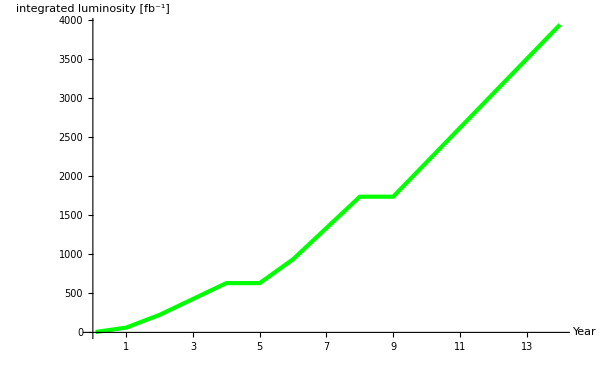

TwoAxisPlot

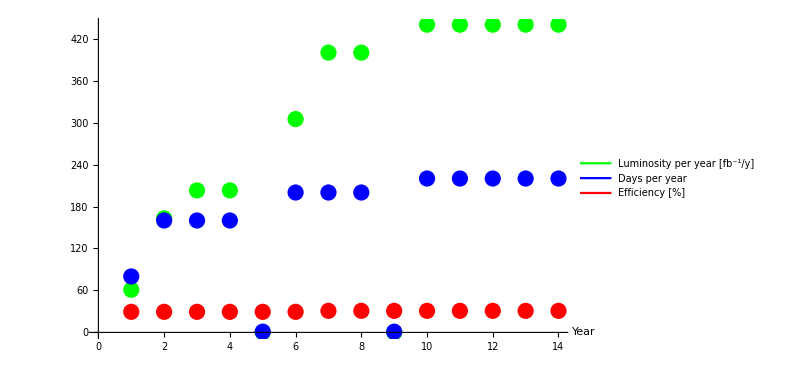

```mathematica
luminosity={{300, 300, 300, 300, 300, 300, 300, 300, 300, 300, 300, 300, 300, 300}};
luminosity={{61, 163, 203, 203, 0, 305, 400, 400, 0, 440, 440, 440, 440, 440}};
lumi=Accumulate[luminosity[[1]]];
lumiramp=List[];
For[i=1,i≤nstep,i++,
If[i≤12,lumiramp=Append[lumiramp,N[lumi[[1]]*step*i]],If[i==nstep,lumiramp=Append[lumiramp,N[lumi[[nyears]]]],lumiramp=Append[lumiramp,N[lumi[[IntegerPart[i*step]]]+(lumi[[IntegerPart[i*step]+1]]-lumi[[IntegerPart[i*step]]])*(i*step-IntegerPart[i*step])]]]];
]
totallumi=Last[lumiramp];
lumiplot=ListPlot[luminosity,AxesLabel->{"Year",""},Ticks->Automatic,plotformat];
intlumiplot=ListLinePlot[lumiramp,AxesLabel->{"Year","integrated luminosity [fb^-1]"},plotformat]
daysperyear = {{120, 120, 120, 120, 120, 120, 120, 120, 120, 120, 120, 120, 120, 120}};
daysperyear = {{80, 160, 160, 160, 1, 200, 200, 200, 1, 220, 220, 220, 220, 220}};
eff = {{0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5}};
eff = {{0.294, 0.294, 0.294, 0.294, 0.294, 0.294, 0.308, 0.308, 0.308, 0.308, 0.308, 0.308, 0.308, 0.308}};
dpyplot=ListPlot[daysperyear,AxesLabel->{"Year","days"},Ticks->Automatic,PlotStyle->{Blue,Thickness[0.005]},plotformat];
effplot=ListPlot[100*eff,AxesLabel->{"Year","days"},Ticks->Automatic,PlotStyle->{Red,Thickness[0.005]},plotformat];
inputplot=TwoAxisPlot
Legended[Show[lumiplot,dpyplot,effplot],Placed[LineLegend[{Green,Blue,Red},{ Style["Luminosity per year [fb^-1/y]",16,Bold],Style["Days per year",16,Bold],Style["Efficiency [%]",16,Bold]},LegendFunction->Framed],{{0.98,0.4},{1,1}}]]
```

Accumulated flux at end of each year for each barrel 
in neq/cm^2 for the four barrels for 3000 fb^-1, calculated by Paul Miyagawa for layout 5.01

```mathematica
totalfluxb1=5.31*10^(14)*(1+safetyfluence);totalfluxb2=3.80*10^(14)*(1+safetyfluence);totalfluxb3=2.86*10^(14)*(1+safetyfluence);totalfluxb4=2.26*10^(14)*(1+safetyfluence);
fluxb1=totalfluxb1/3000*lumiramp;fluxb2=totalfluxb2/3000*lumiramp;fluxb3=totalfluxb3/3000*lumiramp;
fluxb4=totalfluxb4/3000*lumiramp;
```

Total dose rates at representative strip system locations
From ref. xxx total TID in kRad for an integrated luminosity of 3000 fb^-1 for the four barrels, calculated by Paul Miyagawa for layout 5.01

```mathematica
b1TID=23300*(1+safetyfluence);b2TID=12400*(1+safetyfluence);b3TID=6800*(1+safetyfluence);b4TID=3800*(1+safetyfluence);
```

Accumulated TID at end of each year for each barrel

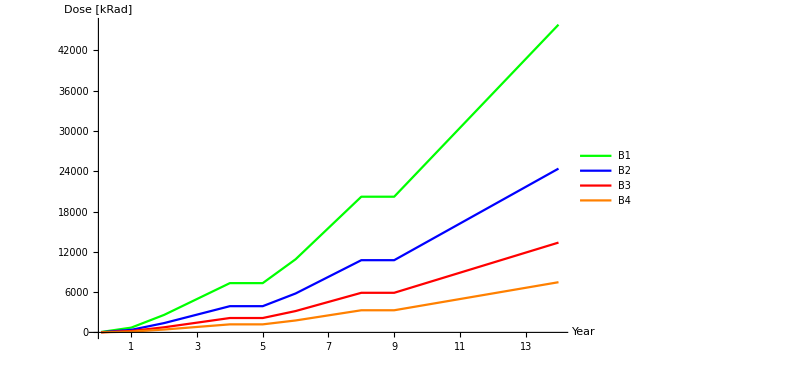

```mathematica
tidb1=N[b1TID/3000*lumiramp];tidb2=N[b2TID/3000*lumiramp];tidb3=N[b3TID/3000*lumiramp];tidb4=N[b4TID/3000*lumiramp];
tidplot=ListLinePlot[{tidb1,tidb2,tidb3,tidb4},AxesLabel->{"Year","Dose [kRad]"},PlotStyle->{Green,Blue,Red, Orange},plotformat,PlotLegends->Placed[LineLegend[{Green,Blue,Red,Orange},{ Style["B1",16,Bold],Style["B2",16,Bold],Style["B3",16,Bold],Style["B4",16,Bold]},LegendFunction->Framed],{{0.3,0.8},{1,1}}]]
```

Dose rate for each year for each barrel

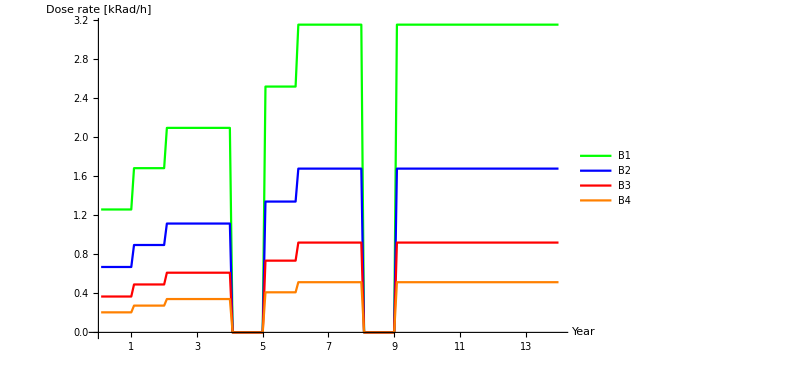

```mathematica
hoursperyear = 24*daysperyear[[1]]*eff[[1]];
doserateb1=List[];doserateb2=List[];doserateb3=List[];doserateb4=List[];
For[i=0,i<nyears,i=i+step,
index=IntegerPart[i]+1;
doserateb1=Append[doserateb1,N[b1TID/3000*Flatten[luminosity][[index]]/hoursperyear[[index]]]];
doserateb2=Append[doserateb2,N[b2TID/3000*Flatten[luminosity][[index]]/hoursperyear[[index]]]];
doserateb3=Append[doserateb3,N[b3TID/3000*Flatten[luminosity][[index]]/hoursperyear[[index]]]];
doserateb4=Append[doserateb4,N[b4TID/3000*Flatten[luminosity][[index]]/hoursperyear[[index]]]];
]
doserateplot=ListLinePlot[{doserateb1,doserateb2,doserateb3,doserateb4},AxesLabel->{"Year","Dose rate [kRad/h]"},PlotStyle->{Green,Blue,Red, Orange},plotformat,PlotLegends->Placed[LineLegend[{Green,Blue,Red,Orange},{ Style["B1",16,Bold],Style["B2",16,Bold],Style["B3",16,Bold],Style["B4",16,Bold]},LegendFunction->Framed],{{0.2,0.99},{1,0.9}}]]
```

12. Sensor leakage
The sensor leakage power Qref  at a reference temperature Tref = -15 °C is derived from measurements of the current density dependent on the fluence j in Neq/cm2  [ref Marcella Mikestikova]

Leakage current as a function of flux
in A/cm2

```mathematica
iref[j_]:=Max[0,(-0.14+3.40*10^(-14)*j)/1000000]
Text[Row[{"Current at reference temperature -15^oC: ",TraditionalForm[iref[j]]}]]
```

Current at reference temperature -15^oC: max(0,(3.4×10^-14 j-0.14)/1000000)

```mathematica
iref700[j_]:=Max[0,(-0.761+4.02*10^(-14)*j)/1000000]
Text[Row[{"Current at reference temperature -15^oC: ",TraditionalForm[iref700[j]]}]]
If[vbiasscale==1.4,iref[j_]=iref700[j]]
```

Current at reference temperature -15^oC: max(0,(4.02×10^-14 j-0.761)/1000000)

```mathematica
Text[Row[{"Current at reference temperature -15^oC: ",TraditionalForm[iref[j]]}]]
```

Current at reference temperature -15^oC: max(0,(3.4×10^-14 j-0.14)/1000000)

```mathematica
oldiref[j_]:=(1.22+2.68*10^(-14)*j)/1000000
Text[Row[{"Current at reference temperature -15^oC: ",TraditionalForm[oldiref[j]]}]]
```

Current at reference temperature -15^oC: (2.68×10^-14 j+1.22)/1000000

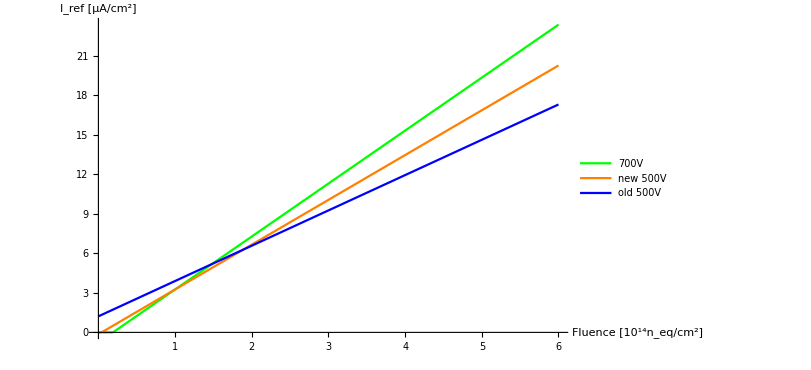

```mathematica
irefplot=Plot[{iref700[x]*1000000,iref[x]*1000000,oldiref[x]*1000000},{x,0,6*10^(14)},AxesLabel->{"Fluence [10^14n_eq/cm^2]" ,"I_ref [μA/cm^2]"},AxesStyle->{Directive[18,Bold],Directive[18,Bold]},ImageSize->600,PlotStyle->{Green,Orange, Blue},Ticks->{{{1*10^(14),"1"},{2*10^(14),"2"},{3*10^(14),"3"},{4*10^(14),"4"},{5*10^(14),"5"},{6*10^(14),"6"}},Automatic},PlotLegends->Placed[LineLegend[{Green,Orange,Blue},{Style["700V",16,Bold], Style["new 500V",16,Bold],Style["old 500V",16,Bold]},LegendFunction->Framed],{{0.4,0.8},{1,0.9}}]]
```

Leakage power per module Barrel 1
in Watt

```mathematica
qrefb1=List[];qrefb2=List[];qrefb3=List[];qrefb4=List[];
For[i=1,i<=nstep,i++,
qrefb1=Append[qrefb1,vbias*iref[fluxb1[[i]]]*area];
qrefb2=Append[qrefb2,vbias*iref[fluxb2[[i]]]*area];
qrefb3=Append[qrefb3,vbias*iref[fluxb3[[i]]]*area];
qrefb4=Append[qrefb4,vbias*iref[fluxb4[[i]]]*area];
]
```

13. Sensor temperature calculation

Barrel 1

```mathematica
(*Initialize lists*)
tsb1=List[];isb1=List[];tabcb1=List[];thccb1=List[];tfeastb1=List[];teosb1=List[];pmoduleb1=List[];
pmtapeb1=List[];pmhvb1=List[];isb1=List[];pmhvrb1=List[];pb1=List[];phvb1=List[];pmhvmuxb1=List[];
itapeb1=List[];idigb1=List[];efffeastb1=List[];ptapeb1=List[];pstaveb1=List[];
(*Initialize temperatures*)
defTeos=ssTeos[sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTabc=ssTabc[ssPabc[nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defThcc=ssThcc[ssPhcc[nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTfeast=ssTfeast[ssPfeast[nomsensorT,nomsensorT,nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
(*calculate temperatures, powers etc.*)
For[i=1,i≤nstep,i++,
sol=FindInstance[
(*solve for qref (with 2 solutions)*)
qrefb1[[i]]==Qref[ts,ssT0[sseosP[If[i==1,defTeos,teosb1[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],ts]/vbias],tc[[i]]]],
ts,Reals,2];
resultts=ts/.sol;(*Print[i,resultts]*);
(*select correct solution*) 
If[Length[resultts]==1,index=1,If[resultts[[1]]>resultts[[2]],index=2,index=1]];
(*calculate temperatures in the system based on sensor temperature*)
(*sensor temperature*)tsb1=Append[tsb1,resultts[[index]]];
(*temperature of ABC*)tabcb1=Append[tabcb1,ssTabc[ssPabc[If[i==1,defTabc,tabcb1[[i-1]]],doserateb1[[i]],tidb1[[i]]],sseosP[If[i==1,defTeos,teosb1[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],resultts[[index]]]/vbias],unref[qrefb1[[i]],resultts[[index]]],tc[[i]]]];
(*temperature of HCC*)
thccb1=Append[thccb1,ssThcc[ssPhcc[If[i==1,defThcc,thccb1[[i-1]]],doserateb1[[i]],tidb1[[i]]],sseosP[If[i==1,defTeos,teosb1[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],resultts[[index]]]/vbias],unref[qrefb1[[i]],resultts[[index]]],tc[[i]]]];
(*temperature of FEAST*)
tfeastb1=Append[tfeastb1,ssTfeast[ssPfeast[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]]],sseosP[If[i==1,defTeos,teosb1[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],resultts[[index]]]/vbias],unref[qrefb1[[i]],resultts[[index]]],tc[[i]]]];
(*temperature of EOS*)
teosb1=Append[teosb1,ssTeos[sseosP[If[i==1,defTeos,teosb1[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb1[[i-1]]],If[i==1,defThcc,thccb1[[i-1]]],If[i==1,defTfeast,tfeastb1[[i-1]]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],resultts[[index]]]/vbias],unref[qrefb1[[i]],resultts[[index]]],tc[[i]]]];
(*from here we can use actual temperatures*)
(*power per module (front-end + HV)*)
pmoduleb1=Append[pmoduleb1,ssPmod[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],tsb1[[i]]]/vbias]+unref[qrefb1[[i]],tsb1[[i]]]];
(*power in tape per module*)
pmtapeb1=Append[pmtapeb1,ssPtape[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],doserateb1[[i]],tidb1[[i]]]];
(*HV power per module (leakage + resistors*)
pmhvb1=Append[pmhvb1,unref[qrefb1[[i]],tsb1[[i]]]+Phv[unref[qrefb1[[i]],tsb1[[i]]]/vbias]];
(*leakage current per module*)
isb1=Append[isb1,unref[qrefb1[[i]],tsb1[[i]]]/vbias];
(*HV power per module due to serial resistors*)
pmhvrb1=Append[pmhvrb1,Prhv[unref[qrefb1[[i]],tsb1[[i]]]/vbias]];
(*HV per module due to parallel resistor*)
pmhvmuxb1=Append[pmhvmuxb1,Phvmux];
(*stave power B1*)
pstaveb1 = Append[pstaveb1,ssPstave[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],teosb1[[i]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],tsb1[[i]]]/vbias]];
(*total power for B1*)
pb1=Append[pb1,2*nstavesb1*(1+safetylayout)/1000*ssPstave[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],teosb1[[i]],doserateb1[[i]],tidb1[[i]],unref[qrefb1[[i]],tsb1[[i]]]/vbias]];
(*total HV power for B1*)
phvb1=Append[phvb1,2*nstavesb1*(1+safetylayout)/1000*2*nmod*(pmhvb1[[i]]+pmhvrb1[[i]])];
(*tape current per module*)
itapeb1=Append[itapeb1,ssItape[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],doserateb1[[i]],tidb1[[i]]]];
(*tape power for one tape (half a stave)*)
ptapeb1=Append[ptapeb1,ssPstavetape[tabcb1[[i]],thccb1[[i]],tfeastb1[[i]],doserateb1[[i]],tidb1[[i]]]];
(*digital current per module*)
idigb1=Append[idigb1,ssIdig[tabcb1[[i]],thccb1[[i]],doserateb1[[i]],tidb1[[i]]]];
(*FEAST efficiency*)
efffeastb1=Append[efffeastb1,feasteff[tfeastb1[[i]],ssIfeast[tabcb1[[i]],thccb1[[i]],doserateb1[[i]],tidb1[[i]]]]];
(*done*)
If[i*step==IntegerPart[i*step],Print["calculated year ",i*step]];
]
```

calculated year 1

calculated year 2

calculated year 3

calculated year 4

calculated year 5

calculated year 6

calculated year 7

calculated year 8

calculated year 9

calculated year 10

calculated year 11

calculated year 12

calculated year 13

calculated year 14

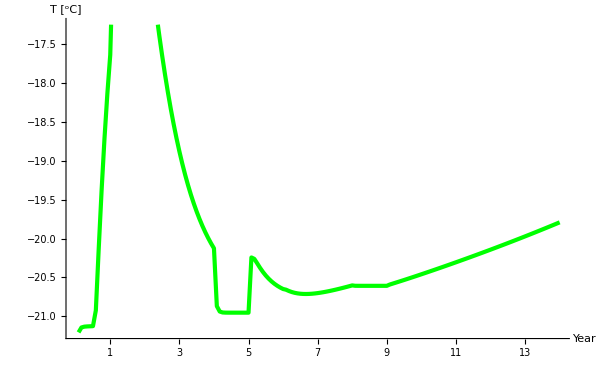

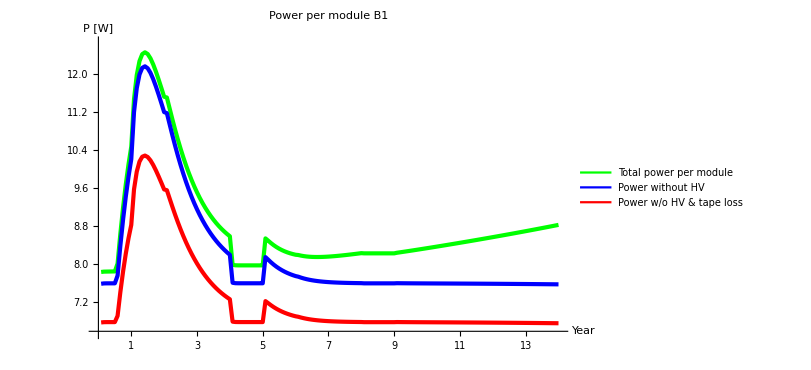

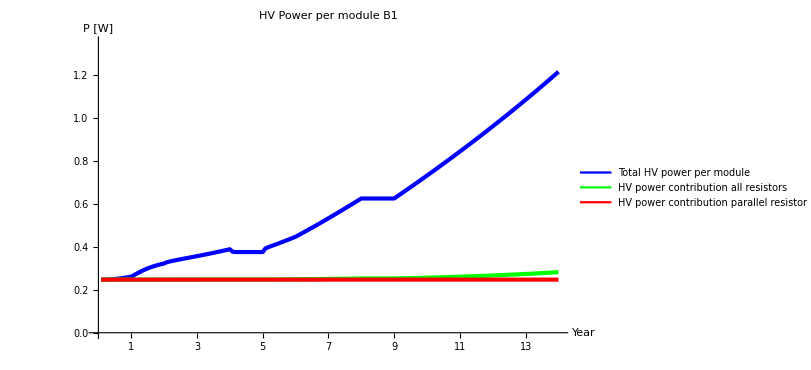

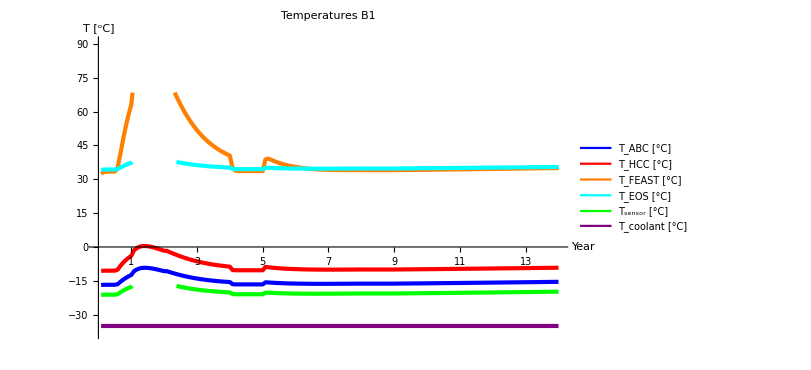

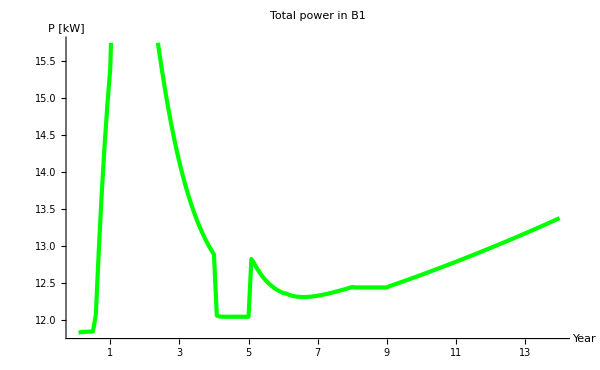

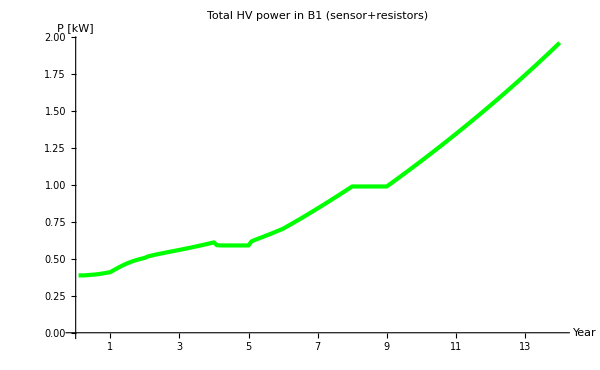

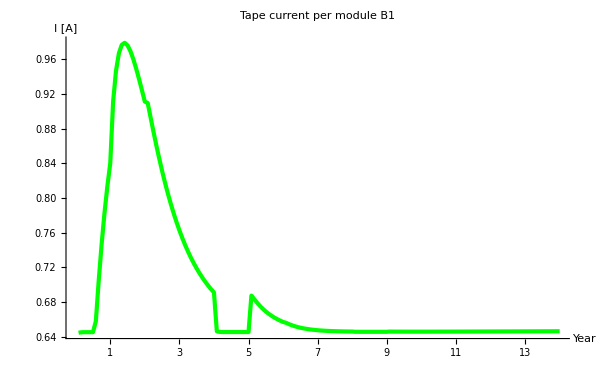

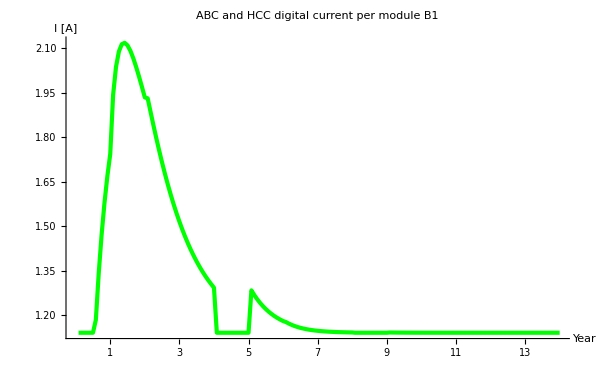

```mathematica
(*plots*)
maxT=Max[tsb1,tabcb1,thccb1,tfeastb1,teosb1,tc]+3;
minT=Min[tsb1,tabcb1,thccb1,tfeastb1,teosb1,tc]-3;
tsb1plot=ListLinePlot[tsb1,AxesLabel->{"Year","T [^oC]"},plotformat]
tabcb1plot=ListLinePlot[tabcb1,AxesLabel->{"Year","T [^oC]"},PlotRange->{{0,168},{minT,maxT}},PlotStyle->{Blue,Thickness[0.005]},plotformat];
thccb1plot=ListLinePlot[thccb1,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
tfeastb1plot=ListLinePlot[tfeastb1,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Orange,Thickness[0.005]},plotformat];
teosb1plot=ListLinePlot[teosb1,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Cyan,Thickness[0.005]},plotformat];
isb1plot=ListLinePlot[isb1,AxesLabel->{"Year","I_S [A]"},plotformat];
maxp=Max[pmoduleb1]+0.2;
minp=Min[pmoduleb1-pmtapeb1-pmhvb1-pmhvrb1]-0.2;
pmodb1plot=ListLinePlot[pmoduleb1,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{minp,maxp}},plotformat];
pmodnohvb1plot=ListLinePlot[pmoduleb1-(pmhvb1+pmhvrb1),AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},plotformat];
pmodnotnohvb1plot=ListLinePlot[pmoduleb1-pmtapeb1-pmhvb1-pmhvrb1,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
pmtapeb1plot=ListLinePlot[pmtapeb1,AxesLabel->{"Year","P [W]"},plotformat];
maxp=Max[pmhvb1,pmhvrb1,pmhvb1+pmhvrb1]+0.1;
minp=Min[pmhvb1,pmhvrb1,pmhvb1+pmhvrb1]-0.1;
pmhvb1plot=ListLinePlot[pmhvb1,AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,168},{0,maxp}},plotformat];
pmhvrb1plot=ListLinePlot[pmhvrb1+pmhvmuxb1,AxesLabel->{"Year","P [W]"},plotformat];
pmhvmuxb1plot=ListLinePlot[pmhvmuxb1,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
Legended[Show[pmodb1plot,pmodnohvb1plot,pmodnotnohvb1plot,PlotLabel->"Power per module B1",LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue,Red},{ Style["Total power per module",16,Bold],Style["Power without HV",16,Bold],Style["Power w/o HV & tape loss",16,Bold]},LegendFunction->Framed],{{0.99,0.95},{1,1}}]]
Legended[Show[pmhvb1plot,pmhvrb1plot,pmhvmuxb1plot,PlotLabel->"HV Power per module B1",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Green,Red},{ Style["Total HV power per module",16,Bold],Style["HV power contribution all resistors",16,Bold],Style["HV power contribution parallel resistor",16,Bold]},LegendFunction->Framed],{{0.99,0.3},{1,1}}]]
Legended[Show[tabcb1plot,thccb1plot,tfeastb1plot,teosb1plot,tsb1plot,Tcoolantplot,PlotLabel->"Temperatures B1",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Red,Orange,Cyan,Green,Purple},{ Style["T_ABC [°C]",16,Bold],Style["T_HCC [°C]",16,Bold],Style["T_FEAST [°C]",16,Bold],Style["T_EOS [°C]",16,Bold],Style["T_sensor [°C]",16,Bold],Style["T_coolant [°C]",16,Bold]},LegendFunction->Framed],{{0.9,0.95},{1,1}}]]
pb1plot=ListLinePlot[pb1,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total power in B1",Bold,24],plotformat]
phvb1plot=ListLinePlot[phvb1,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total HV power in B1 (sensor+resistors)",Bold,24],plotformat]
itapeb1plot=ListLinePlot[itapeb1,AxesLabel->{"Year","I [A]"},PlotLabel->Style["Tape current per module B1",Bold,24],plotformat]
idigb1plot=ListLinePlot[idigb1,AxesLabel->{"Year","I [A]"},PlotLabel->Style["ABC and HCC digital current per module B1",Bold,24],plotformat]
efffeastb1plot=ListLinePlot[efffeastb1,AxesLabel->{"Year","Efficiency [%]"},PlotLabel->Style["Feast efficiency B1",Bold,24],plotformat]
ptapeb1plot=ListLinePlot[ptapeb1,AxesLabel->{"Year","Power [W]"},PlotLabel->Style["Power loss in complete tape B1",Bold,24],plotformat]
```

Barrel 2

```mathematica
(*Initialize lists*)
tsb2=List[];isb2=List[];tabcb2=List[];thccb2=List[];tfeastb2=List[];teosb2=List[];pmoduleb2=List[];
pmtapeb2=List[];pmhvb2=List[];isb2=List[];pmhvrb2=List[];pb2=List[];phvb2=List[];pmhvmuxb2=List[];
itapeb2=List[];idigb2=List[];pstaveb2=List[];
(*Initialize temperatures*)
defTeos=ssTeos[sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTabc=ssTabc[ssPabc[nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defThcc=ssThcc[ssPhcc[nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTfeast=ssTfeast[ssPfeast[nomsensorT,nomsensorT,nomsensorT,1,0],sseosP[nomsensorT],ssPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
(*calculate temperatures, powers etc.*)
For[i=1,i≤nstep,i++,
sol=FindInstance[
(*solve for qref (with 2 solutions)*)
qrefb2[[i]]==Qref[ts,ssT0[sseosP[If[i==1,defTeos,teosb2[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],ts]/vbias],tc[[i]]]],
ts,Reals,2];
resultts=ts/.sol;(*Print[i,resultts]*);
(*select correct solution*) 
If[Length[resultts]==1,index=1,If[resultts[[1]]>resultts[[2]],index=2,index=1]];
(*calculate temperatures in the system based on sensor temperature*)
tsb2=Append[tsb2,resultts[[index]]];
tabcb2=Append[tabcb2,ssTabc[ssPabc[If[i==1,defTabc,tabcb2[[i-1]]],doserateb2[[i]],tidb2[[i]]],sseosP[If[i==1,defTeos,teosb2[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],resultts[[index]]]/vbias],unref[qrefb2[[i]],resultts[[index]]],tc[[i]]]];
thccb2=Append[thccb2,ssThcc[ssPhcc[If[i==1,defThcc,thccb2[[i-1]]],doserateb2[[i]],tidb2[[i]]],sseosP[If[i==1,defTeos,teosb2[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],resultts[[index]]]/vbias],unref[qrefb2[[i]],resultts[[index]]],tc[[i]]]];
tfeastb2=Append[tfeastb2,ssTfeast[ssPfeast[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]]],sseosP[If[i==1,defTeos,teosb2[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],resultts[[index]]]/vbias],unref[qrefb2[[i]],resultts[[index]]],tc[[i]]]];
teosb2=Append[teosb2,ssTeos[sseosP[If[i==1,defTeos,teosb2[[i-1]]]],ssPmod[If[i==1,defTabc,tabcb2[[i-1]]],If[i==1,defThcc,thccb2[[i-1]]],If[i==1,defTfeast,tfeastb2[[i-1]]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],resultts[[index]]]/vbias],unref[qrefb2[[i]],resultts[[index]]],tc[[i]]]];
(*from here we can use actual temperatures*)
pmoduleb2=Append[pmoduleb2,ssPmod[tabcb2[[i]],thccb2[[i]],tfeastb2[[i]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],tsb2[[i]]]/vbias]+unref[qrefb2[[i]],tsb2[[i]]]];
pmtapeb2=Append[pmtapeb2,ssPtape[tabcb2[[i]],thccb2[[i]],tfeastb2[[i]],doserateb2[[i]],tidb2[[i]]]];
pmhvb2=Append[pmhvb2,unref[qrefb2[[i]],tsb2[[i]]]+Phv[unref[qrefb2[[i]],tsb2[[i]]]/vbias]];
isb2=Append[isb2,unref[qrefb2[[i]],tsb2[[i]]]/vbias];
pmhvrb2=Append[pmhvrb2,Prhv[unref[qrefb2[[i]],tsb2[[i]]]/vbias]];
pmhvmuxb2=Append[pmhvmuxb2,Phvmux];
pstaveb2= Append[pstaveb2,ssPstave[tabcb2[[i]],thccb2[[i]],tfeastb2[[i]],teosb2[[i]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],tsb2[[i]]]/vbias]];
pb2=Append[pb2,2*nstavesb2*(1+safetylayout)/1000*ssPstave[tabcb2[[i]],thccb2[[i]],tfeastb2[[i]],teosb2[[i]],doserateb2[[i]],tidb2[[i]],unref[qrefb2[[i]],tsb2[[i]]]/vbias]];
phvb2=Append[phvb2,2*nstavesb2*(1+safetylayout)/1000*2*nmod*(pmhvb2[[i]]+pmhvrb2[[i]])];
itapeb2=Append[itapeb2,ssItape[tabcb2[[i]],thccb2[[i]],tfeastb2[[i]],doserateb2[[i]],tidb2[[i]]]];
idigb2=Append[idigb2,ssIdig[tabcb2[[i]],thccb2[[i]],doserateb2[[i]],tidb2[[i]]]];
(*done*)
If[i*step==IntegerPart[i*step],Print["calculated year ",i*step]];
]
```

calculated year 1

calculated year 2

calculated year 3

calculated year 4

calculated year 5

calculated year 6

calculated year 7

calculated year 8

calculated year 9

calculated year 10

calculated year 11

calculated year 12

calculated year 13

calculated year 14

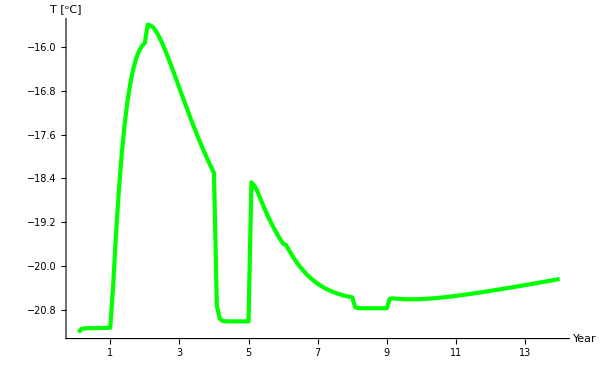

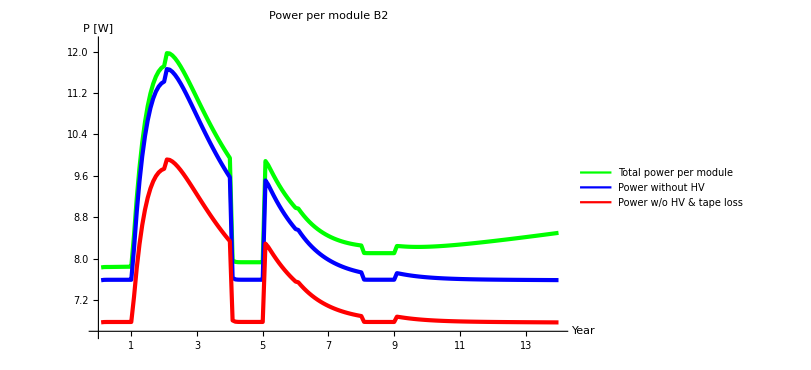

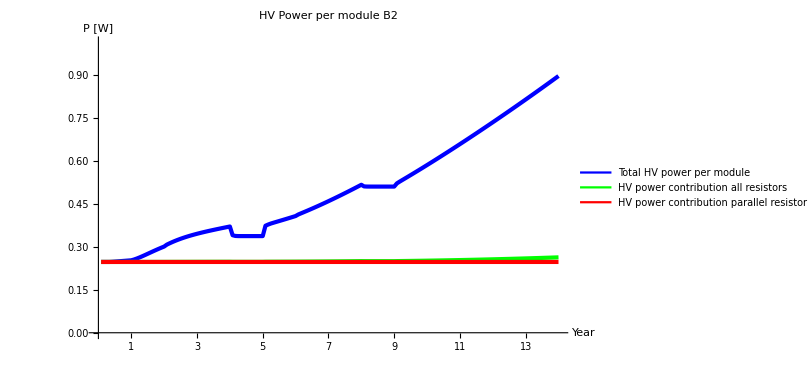

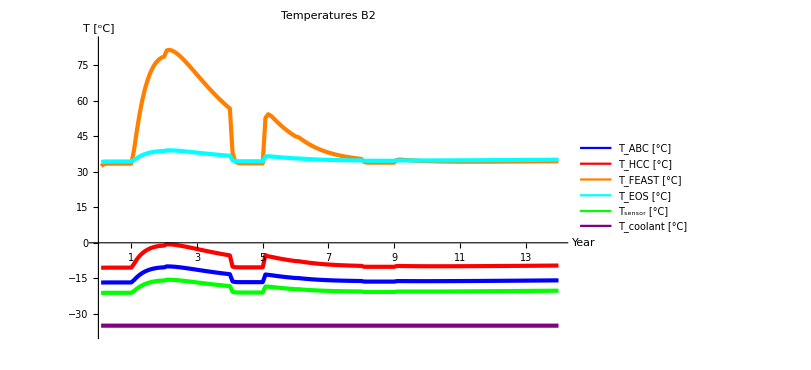

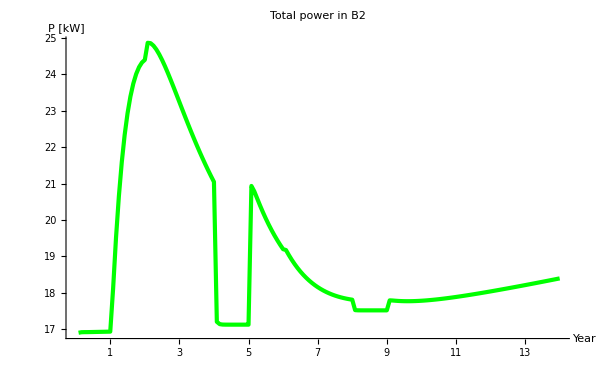

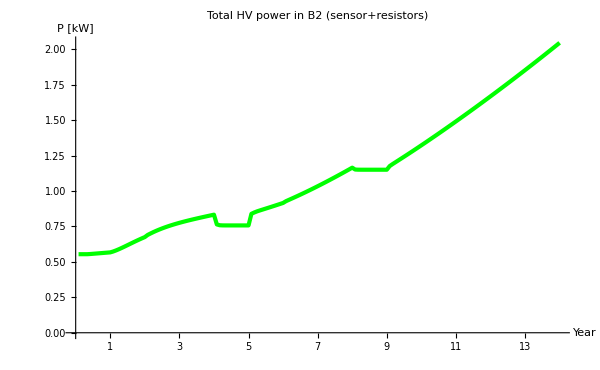

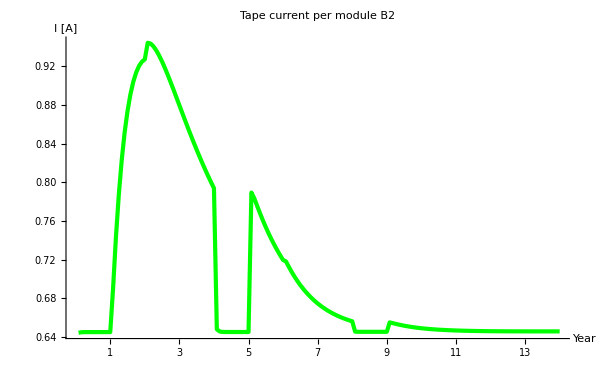

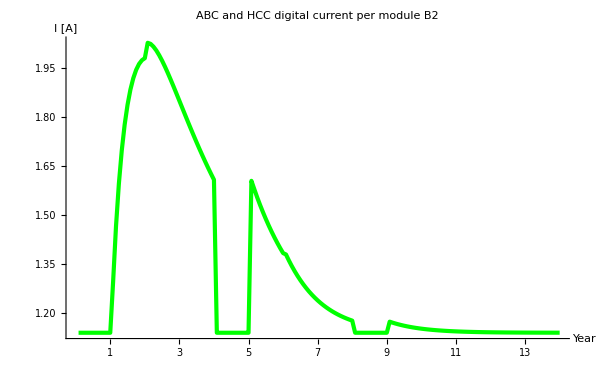

```mathematica
(*plots*)
maxT=Max[tsb2,tabcb2,thccb2,tfeastb2,teosb2,tc]+3;
minT=Min[tsb2,tabcb2,thccb2,tfeastb2,teosb2,tc]-3;
tsb2plot=ListLinePlot[tsb2,AxesLabel->{"Year","T [^oC]"},plotformat]
tabcb2plot=ListLinePlot[tabcb2,AxesLabel->{"Year","T [^oC]"},PlotRange->{{0,168},{minT,maxT}},PlotStyle->{Blue,Thickness[0.005]},plotformat];
thccb2plot=ListLinePlot[thccb2,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
tfeastb2plot=ListLinePlot[tfeastb2,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Orange,Thickness[0.005]},plotformat];
teosb2plot=ListLinePlot[teosb2,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Cyan,Thickness[0.005]},plotformat];
isb2plot=ListLinePlot[isb2,AxesLabel->{"Year","I_S [A]"},plotformat];
maxp=Max[pmoduleb2]+0.2;
minp=Min[pmoduleb2-pmtapeb2-pmhvb2-pmhvrb2]-0.2;
pmodb2plot=ListLinePlot[pmoduleb2,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{minp,maxp}},plotformat];
pmodnohvb2plot=ListLinePlot[pmoduleb2-(pmhvb2+pmhvrb2),AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},plotformat];
pmodnotnohvb2plot=ListLinePlot[pmoduleb2-pmtapeb2-pmhvb2-pmhvrb2,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
pmtapeb2plot=ListLinePlot[pmtapeb2,AxesLabel->{"Year","P [W]"},plotformat];
maxp=Max[pmhvb2,pmhvrb2,pmhvb2+pmhvrb2]+0.1;
minp=Min[pmhvb2,pmhvrb2,pmhvb2+pmhvrb2]-0.1;
pmhvb2plot=ListLinePlot[pmhvb2,AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,168},{0,maxp}},plotformat];
pmhvrb2plot=ListLinePlot[pmhvrb2+pmhvmuxb2,AxesLabel->{"Year","P [W]"},plotformat];
pmhvmuxb2plot=ListLinePlot[pmhvmuxb2,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
Legended[Show[pmodb2plot,pmodnohvb2plot,pmodnotnohvb2plot,PlotLabel->"Power per module B2",LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue,Red},{ Style["Total power per module",16,Bold],Style["Power without HV",16,Bold],Style["Power w/o HV & tape loss",16,Bold]},LegendFunction->Framed],{{0.99,0.95},{1,1}}]]
Legended[Show[pmhvb2plot,pmhvrb2plot,pmhvmuxb2plot,PlotLabel->"HV Power per module B2",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Green,Red},{ Style["Total HV power per module",16,Bold],Style["HV power contribution all resistors",16,Bold],Style["HV power contribution parallel resistor",16,Bold]},LegendFunction->Framed],{{0.99,0.3},{1,1}}]]
Legended[Show[tabcb2plot,thccb2plot,tfeastb2plot,teosb2plot,tsb2plot,Tcoolantplot,PlotLabel->"Temperatures B2",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Red,Orange,Cyan,Green,Purple},{ Style["T_ABC [°C]",16,Bold],Style["T_HCC [°C]",16,Bold],Style["T_FEAST [°C]",16,Bold],Style["T_EOS [°C]",16,Bold],Style["T_sensor [°C]",16,Bold],Style["T_coolant [°C]",16,Bold]},LegendFunction->Framed],{{0.9,0.95},{1,1}}]]
pb2plot=ListLinePlot[pb2,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total power in B2",Bold,24],plotformat]
phvb2plot=ListLinePlot[phvb2,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total HV power in B2 (sensor+resistors)",Bold,24],plotformat]
itapeb2plot=ListLinePlot[itapeb2,AxesLabel->{"Year","I [A]"},PlotLabel->Style["Tape current per module B2",Bold,24],plotformat]
idigb2plot=ListLinePlot[idigb2,AxesLabel->{"Year","I [A]"},PlotLabel->Style["ABC and HCC digital current per module B2",Bold,24],plotformat]
```

Barrel 3

```mathematica
(*Initialize lists*)
tsb3=List[];isb3=List[];tabcb3=List[];thccb3=List[];tfeastb3=List[];teosb3=List[];pmoduleb3=List[];
pmtapeb3=List[];pmhvb3=List[];isb3=List[];pmhvrb3=List[];pb3=List[];phvb3=List[];pmhvmuxb3=List[];
itapeb3=List[];idigb3=List[];pstaveb3=List[];
(*Initialize temperatures*)
defTeos=lsTeos[lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTabc=lsTabc[lsPabc[nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defThcc=lsThcc[lsPhcc[nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTfeast=lsTfeast[lsPfeast[nomsensorT,nomsensorT,nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
(*calculate temperatures, powers etc.*)
For[i=1,i≤nstep,i++,
sol=FindInstance[
(*solve for qref (with 2 solutions)*)
qrefb3[[i]]==Qref[ts,lsT0[lseosP[If[i==1,defTeos,teosb3[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],ts]/vbias],tc[[i]]]],
ts,Reals,2];
resultts=ts/.sol;(*Print[i,resultts]*);
(*select correct solution*) 
If[Length[resultts]==1,index=1,If[resultts[[1]]>resultts[[2]],index=2,index=1]];
(*calculate temperatures in the system based on sensor temperature*)
tsb3=Append[tsb3,resultts[[index]]];
tabcb3=Append[tabcb3,lsTabc[lsPabc[If[i==1,defTabc,tabcb3[[i-1]]],doserateb3[[i]],tidb3[[i]]],lseosP[If[i==1,defTeos,teosb3[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],resultts[[index]]]/vbias],unref[qrefb3[[i]],resultts[[index]]],tc[[i]]]];
thccb3=Append[thccb3,lsThcc[lsPhcc[If[i==1,defThcc,thccb3[[i-1]]],doserateb3[[i]],tidb3[[i]]],lseosP[If[i==1,defTeos,teosb3[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],resultts[[index]]]/vbias],unref[qrefb3[[i]],resultts[[index]]],tc[[i]]]];
tfeastb3=Append[tfeastb3,lsTfeast[lsPfeast[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]]],lseosP[If[i==1,defTeos,teosb3[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],resultts[[index]]]/vbias],unref[qrefb3[[i]],resultts[[index]]],tc[[i]]]];
teosb3=Append[teosb3,lsTeos[lseosP[If[i==1,defTeos,teosb3[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb3[[i-1]]],If[i==1,defThcc,thccb3[[i-1]]],If[i==1,defTfeast,tfeastb3[[i-1]]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],resultts[[index]]]/vbias],unref[qrefb3[[i]],resultts[[index]]],tc[[i]]]];
(*from here we can use actual temperatures*)
pmoduleb3=Append[pmoduleb3,lsPmod[tabcb3[[i]],thccb3[[i]],tfeastb3[[i]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],tsb3[[i]]]/vbias]+unref[qrefb3[[i]],tsb3[[i]]]];
pmtapeb3=Append[pmtapeb3,lsPtape[tabcb3[[i]],thccb3[[i]],tfeastb3[[i]],doserateb3[[i]],tidb3[[i]]]];
pmhvb3=Append[pmhvb3,unref[qrefb3[[i]],tsb3[[i]]]+Phv[unref[qrefb3[[i]],tsb3[[i]]]/vbias]];
isb3=Append[isb3,unref[qrefb3[[i]],tsb3[[i]]]/vbias];
pmhvrb3=Append[pmhvrb3,Prhv[unref[qrefb3[[i]],tsb3[[i]]]/vbias]];
pmhvmuxb3=Append[pmhvmuxb3,Phvmux];
pstaveb3= Append[pstaveb3,lsPstave[tabcb3[[i]],thccb3[[i]],tfeastb3[[i]],teosb3[[i]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],tsb3[[i]]]/vbias]];
pb3=Append[pb3,2*nstavesb3*(1+safetylayout)/1000*lsPstave[tabcb3[[i]],thccb3[[i]],tfeastb3[[i]],teosb3[[i]],doserateb3[[i]],tidb3[[i]],unref[qrefb3[[i]],tsb3[[i]]]/vbias]];
phvb3=Append[phvb3,2*nstavesb3*(1+safetylayout)/1000*2*nmod*(pmhvb3[[i]]+pmhvrb3[[i]])];
itapeb3=Append[itapeb3,lsItape[tabcb3[[i]],thccb3[[i]],tfeastb3[[i]],doserateb3[[i]],tidb3[[i]]]];
idigb3=Append[idigb3,lsIdig[tabcb3[[i]],thccb3[[i]],doserateb3[[i]],tidb3[[i]]]];
(*done*)
If[i*step==IntegerPart[i*step],Print["calculated year ",i*step]];
]
```

calculated year 1

calculated year 2

calculated year 3

calculated year 4

calculated year 5

calculated year 6

calculated year 7

calculated year 8

calculated year 9

calculated year 10

calculated year 11

calculated year 12

calculated year 13

calculated year 14

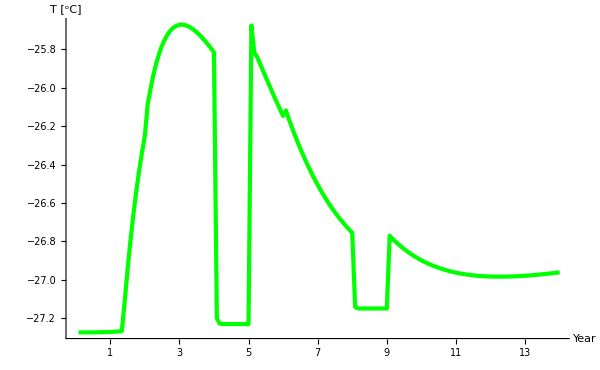

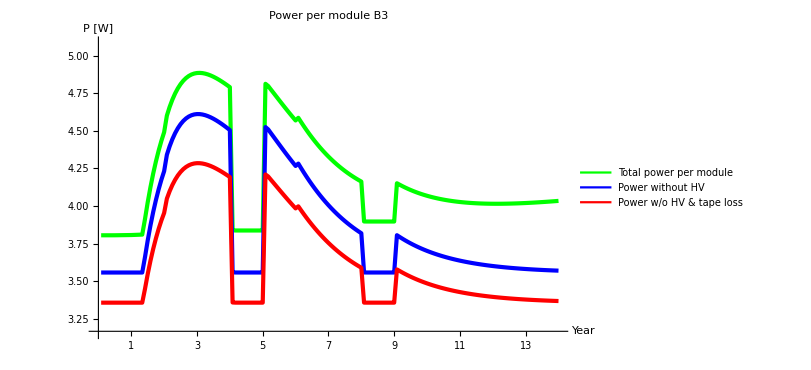

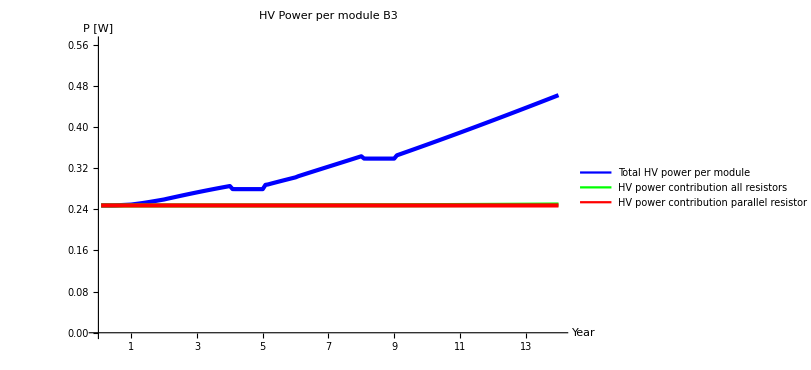

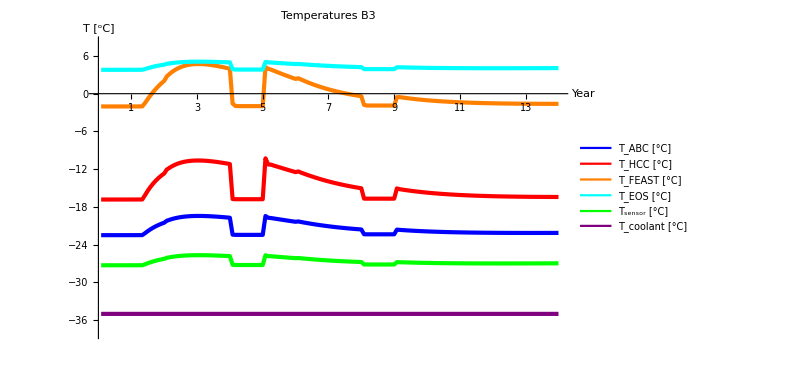

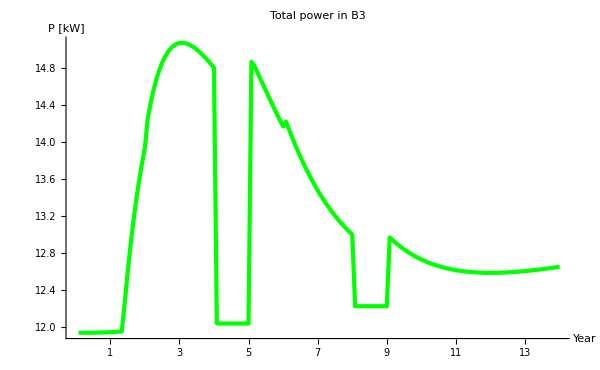

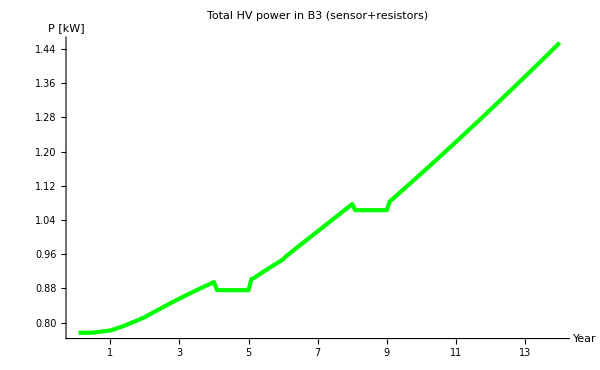

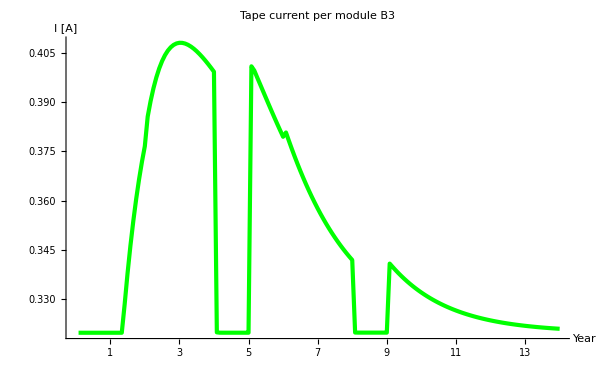

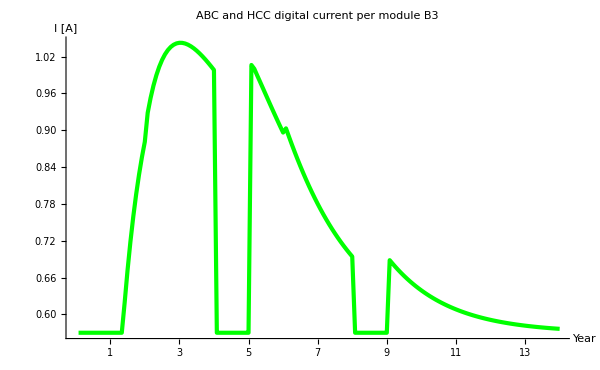

```mathematica
(*plots*)
maxT=Max[tsb3,tabcb3,thccb3,tfeastb3,teosb3,tc]+3;
minT=Min[tsb3,tabcb3,thccb3,tfeastb3,teosb3,tc]-3;
tsb3plot=ListLinePlot[tsb3,AxesLabel->{"Year","T [^oC]"},plotformat]
tabcb3plot=ListLinePlot[tabcb3,AxesLabel->{"Year","T [^oC]"},PlotRange->{{0,168},{minT,maxT}},PlotStyle->{Blue,Thickness[0.005]},plotformat];
thccb3plot=ListLinePlot[thccb3,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
tfeastb3plot=ListLinePlot[tfeastb3,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Orange,Thickness[0.005]},plotformat];
teosb3plot=ListLinePlot[teosb3,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Cyan,Thickness[0.005]},plotformat];
isb3plot=ListLinePlot[isb3,AxesLabel->{"Year","I_S [A]"},plotformat];
maxp=Max[pmoduleb3]+0.2;
minp=Min[pmoduleb3-pmtapeb3-pmhvb3-pmhvrb3]-0.2;
pmodb3plot=ListLinePlot[pmoduleb3,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{minp,maxp}},plotformat];
pmodnohvb3plot=ListLinePlot[pmoduleb3-(pmhvb3+pmhvrb3),AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},plotformat];
pmodnotnohvb3plot=ListLinePlot[pmoduleb3-pmtapeb3-pmhvb3-pmhvrb3,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
pmtapeb3plot=ListLinePlot[pmtapeb3,AxesLabel->{"Year","P [W]"},plotformat];
maxp=Max[pmhvb3,pmhvrb3,pmhvb3+pmhvrb3]+0.1;
minp=Min[pmhvb3,pmhvrb3,pmhvb3+pmhvrb3]-0.1;
pmhvb3plot=ListLinePlot[pmhvb3,AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,168},{0,maxp}},plotformat];
pmhvrb3plot=ListLinePlot[pmhvrb3+pmhvmuxb3,AxesLabel->{"Year","P [W]"},plotformat];
pmhvmuxb3plot=ListLinePlot[pmhvmuxb3,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
Legended[Show[pmodb3plot,pmodnohvb3plot,pmodnotnohvb3plot,PlotLabel->"Power per module B3",LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue,Red},{ Style["Total power per module",16,Bold],Style["Power without HV",16,Bold],Style["Power w/o HV & tape loss",16,Bold]},LegendFunction->Framed],{{0.99,0.95},{1,1}}]]
Legended[Show[pmhvb3plot,pmhvrb3plot,pmhvmuxb3plot,PlotLabel->"HV Power per module B3",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Green,Red},{ Style["Total HV power per module",16,Bold],Style["HV power contribution all resistors",16,Bold],Style["HV power contribution parallel resistor",16,Bold]},LegendFunction->Framed],{{0.99,0.3},{1,1}}]]
Legended[Show[tabcb3plot,thccb3plot,tfeastb3plot,teosb3plot,tsb3plot,Tcoolantplot,PlotLabel->"Temperatures B3",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Red,Orange,Cyan,Green,Purple},{ Style["T_ABC [°C]",16,Bold],Style["T_HCC [°C]",16,Bold],Style["T_FEAST [°C]",16,Bold],Style["T_EOS [°C]",16,Bold],Style["T_sensor [°C]",16,Bold],Style["T_coolant [°C]",16,Bold]},LegendFunction->Framed],{{0.9,0.95},{1,1}}]]
pb3plot=ListLinePlot[pb3,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total power in B3",Bold,24],plotformat]
phvb3plot=ListLinePlot[phvb3,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total HV power in B3 (sensor+resistors)",Bold,24],plotformat]
itapeb3plot=ListLinePlot[itapeb3,AxesLabel->{"Year","I [A]"},PlotLabel->Style["Tape current per module B3",Bold,24],plotformat]
idigb3plot=ListLinePlot[idigb3,AxesLabel->{"Year","I [A]"},PlotLabel->Style["ABC and HCC digital current per module B3",Bold,24],plotformat]
```

Barrel 4

```mathematica
(*Initialize lists*)
tsb4=List[];isb4=List[];tabcb4=List[];thccb4=List[];tfeastb4=List[];teosb4=List[];pmoduleb4=List[];
pmtapeb4=List[];pmhvb4=List[];isb4=List[];pmhvrb4=List[];pb4=List[];phvb4=List[];pmhvmuxb4=List[];
itapeb4=List[];idigb4=List[];pstaveb4=List[];
(*Initialize temperatures*)
defTeos=lsTeos[lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTabc=lsTabc[lsPabc[nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defThcc=lsThcc[lsPhcc[nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
defTfeast=lsTfeast[lsPfeast[nomsensorT,nomsensorT,nomsensorT,1,0],lseosP[nomsensorT],lsPmod[nomsensorT,nomsensorT,nomsensorT,1,0,0],0,tc[[1]]];
(*calculate temperatures, powers etc.*)
For[i=1,i≤nstep,i++,
sol=FindInstance[
(*solve for qref (with 2 solutions)*)
qrefb4[[i]]==Qref[ts,lsT0[lseosP[If[i==1,defTeos,teosb4[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],ts]/vbias],tc[[i]]]],
ts,Reals,2];
resultts=ts/.sol;(*Print[i,resultts]*);
(*select correct solution*) 
If[Length[resultts]==1,index=1,If[resultts[[1]]>resultts[[2]],index=2,index=1]];
(*calculate temperatures in the system based on sensor temperature*)
tsb4=Append[tsb4,resultts[[index]]];
tabcb4=Append[tabcb4,lsTabc[lsPabc[If[i==1,defTabc,tabcb4[[i-1]]],doserateb4[[i]],tidb4[[i]]],lseosP[If[i==1,defTeos,teosb4[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],resultts[[index]]]/vbias],unref[qrefb4[[i]],resultts[[index]]],tc[[i]]]];
thccb4=Append[thccb4,lsThcc[lsPhcc[If[i==1,defThcc,thccb4[[i-1]]],doserateb4[[i]],tidb4[[i]]],lseosP[If[i==1,defTeos,teosb4[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],resultts[[index]]]/vbias],unref[qrefb4[[i]],resultts[[index]]],tc[[i]]]];
tfeastb4=Append[tfeastb4,lsTfeast[lsPfeast[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]]],lseosP[If[i==1,defTeos,teosb4[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],resultts[[index]]]/vbias],unref[qrefb4[[i]],resultts[[index]]],tc[[i]]]];
teosb4=Append[teosb4,lsTeos[lseosP[If[i==1,defTeos,teosb4[[i-1]]]],lsPmod[If[i==1,defTabc,tabcb4[[i-1]]],If[i==1,defThcc,thccb4[[i-1]]],If[i==1,defTfeast,tfeastb4[[i-1]]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],resultts[[index]]]/vbias],unref[qrefb4[[i]],resultts[[index]]],tc[[i]]]];
(*from here we can use actual temperatures*)
pmoduleb4=Append[pmoduleb4,lsPmod[tabcb4[[i]],thccb4[[i]],tfeastb4[[i]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],tsb4[[i]]]/vbias]+unref[qrefb4[[i]],tsb4[[i]]]];
pmtapeb4=Append[pmtapeb4,lsPtape[tabcb4[[i]],thccb4[[i]],tfeastb4[[i]],doserateb4[[i]],tidb4[[i]]]];
pmhvb4=Append[pmhvb4,unref[qrefb4[[i]],tsb4[[i]]]+Phv[unref[qrefb4[[i]],tsb4[[i]]]/vbias]];
isb4=Append[isb4,unref[qrefb4[[i]],tsb4[[i]]]/vbias];
pmhvrb4=Append[pmhvrb4,Prhv[unref[qrefb4[[i]],tsb4[[i]]]/vbias]];
pmhvmuxb4=Append[pmhvmuxb4,Phvmux];
pstaveb4= Append[pstaveb4,lsPstave[tabcb4[[i]],thccb4[[i]],tfeastb4[[i]],teosb4[[i]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],tsb4[[i]]]/vbias]];
pb4=Append[pb4,2*nstavesb4*(1+safetylayout)/1000*lsPstave[tabcb4[[i]],thccb4[[i]],tfeastb4[[i]],teosb4[[i]],doserateb4[[i]],tidb4[[i]],unref[qrefb4[[i]],tsb4[[i]]]/vbias]];
phvb4=Append[phvb4,2*nstavesb4*(1+safetylayout)/1000*2*nmod*(pmhvb4[[i]]+pmhvrb4[[i]])];
itapeb4=Append[itapeb4,lsItape[tabcb4[[i]],thccb4[[i]],tfeastb4[[i]],doserateb4[[i]],tidb4[[i]]]];
idigb4=Append[idigb4,lsIdig[tabcb4[[i]],thccb4[[i]],doserateb4[[i]],tidb4[[i]]]];
(*done*)
If[i*step==IntegerPart[i*step],Print["calculated year ",i*step]];
]
```

calculated year 1

calculated year 2

calculated year 3

calculated year 4

calculated year 5

calculated year 6

calculated year 7

calculated year 8

calculated year 9

calculated year 10

calculated year 11

calculated year 12

calculated year 13

calculated year 14

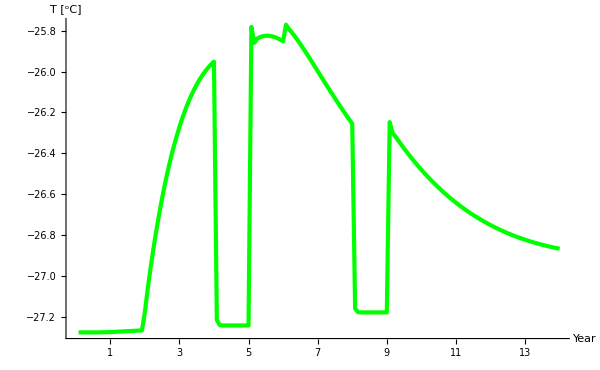

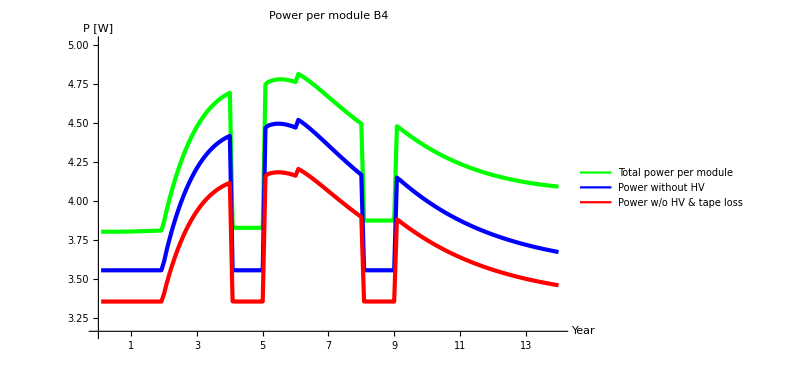

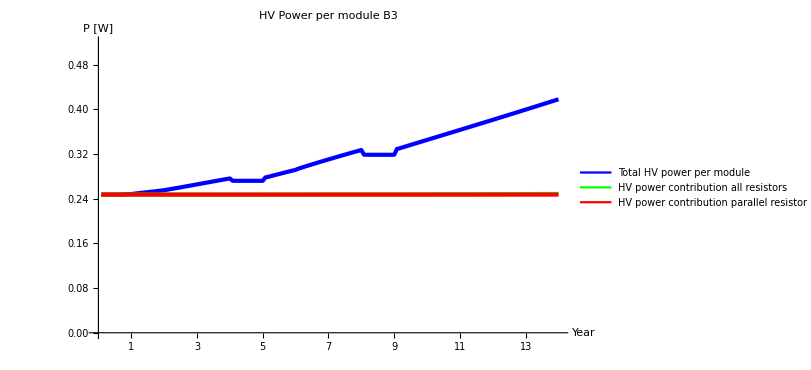

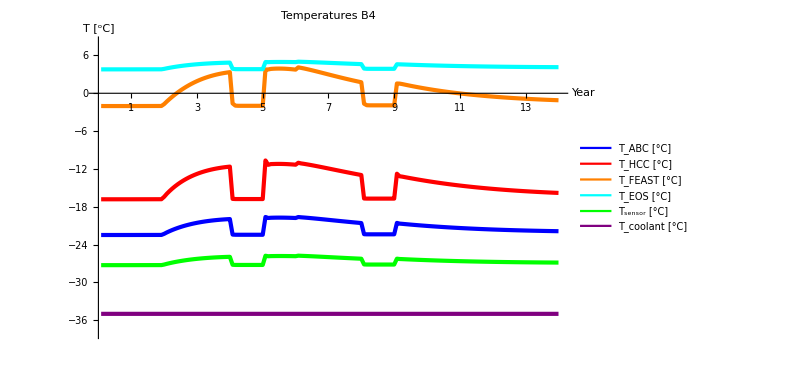

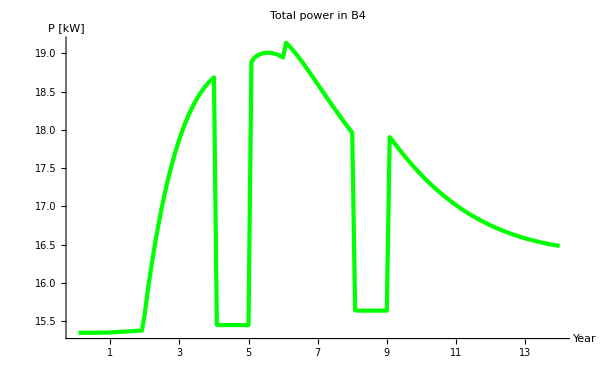

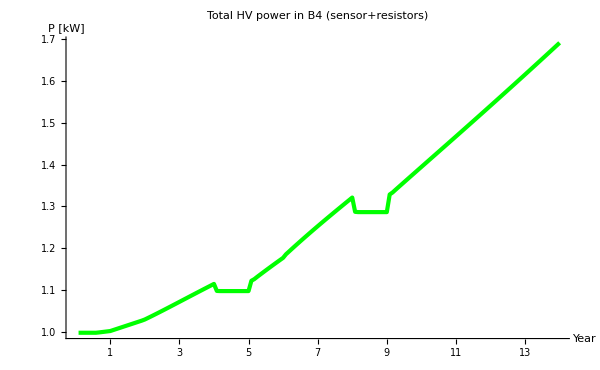

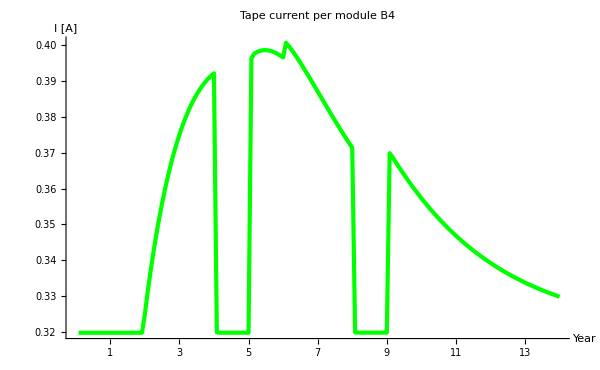

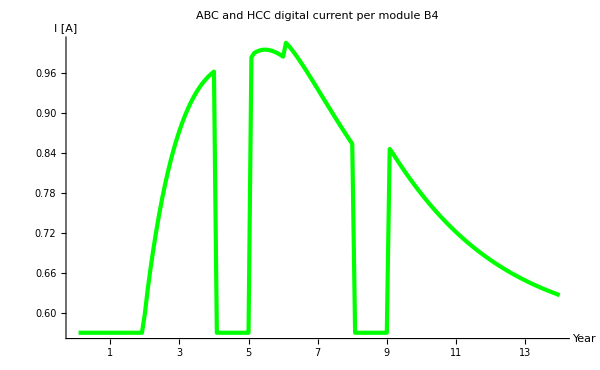

```mathematica
(*plots*)
maxT=Max[tsb4,tabcb4,thccb4,tfeastb4,teosb4,tc]+3;
minT=Min[tsb4,tabcb4,thccb4,tfeastb4,teosb4,tc]-3;
tsb4plot=ListLinePlot[tsb4,AxesLabel->{"Year","T [^oC]"},plotformat]
tabcb4plot=ListLinePlot[tabcb4,AxesLabel->{"Year","T [^oC]"},PlotRange->{{0,168},{minT,maxT}},PlotStyle->{Blue,Thickness[0.005]},plotformat];
thccb4plot=ListLinePlot[thccb4,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
tfeastb4plot=ListLinePlot[tfeastb4,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Orange,Thickness[0.005]},plotformat];
teosb4plot=ListLinePlot[teosb4,AxesLabel->{"Year","T [^oC]"},PlotStyle->{Cyan,Thickness[0.005]},plotformat];
isb4plot=ListLinePlot[isb4,AxesLabel->{"Year","I_S [A]"},plotformat];
maxp=Max[pmoduleb4]+0.2;
minp=Min[pmoduleb4-pmtapeb4-pmhvb4-pmhvrb4]-0.2;
pmodb4plot=ListLinePlot[pmoduleb4,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{minp,maxp}},plotformat];
pmodnohvb4plot=ListLinePlot[pmoduleb4-(pmhvb4+pmhvrb4),AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},plotformat];
pmodnotnohvb4plot=ListLinePlot[pmoduleb4-pmtapeb4-pmhvb4-pmhvrb4,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
pmtapeb4plot=ListLinePlot[pmtapeb4,AxesLabel->{"Year","P [W]"},plotformat];
maxp=Max[pmhvb4,pmhvrb4,pmhvb4+pmhvrb4]+0.1;
minp=Min[pmhvb4,pmhvrb4,pmhvb4+pmhvrb4]-0.1;
pmhvb4plot=ListLinePlot[pmhvb4,AxesLabel->{"Year","P [W]"},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{0,168},{0,maxp}},plotformat];
pmhvrb4plot=ListLinePlot[pmhvrb4+pmhvmuxb4,AxesLabel->{"Year","P [W]"},plotformat];
pmhvmuxb4plot=ListLinePlot[pmhvmuxb4,AxesLabel->{"Year","P [W]"},PlotStyle->{Red,Thickness[0.005]},plotformat];
Legended[Show[pmodb4plot,pmodnohvb4plot,pmodnotnohvb4plot,PlotLabel->"Power per module B4",LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue,Red},{ Style["Total power per module",16,Bold],Style["Power without HV",16,Bold],Style["Power w/o HV & tape loss",16,Bold]},LegendFunction->Framed],{{0.99,0.95},{1,1}}]]
Legended[Show[pmhvb4plot,pmhvrb4plot,pmhvmuxb4plot,PlotLabel->"HV Power per module B3",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Green,Red},{ Style["Total HV power per module",16,Bold],Style["HV power contribution all resistors",16,Bold],Style["HV power contribution parallel resistor",16,Bold]},LegendFunction->Framed],{{0.99,0.3},{1,1}}]]
Legended[Show[tabcb4plot,thccb4plot,tfeastb4plot,teosb4plot,tsb4plot,Tcoolantplot,PlotLabel->"Temperatures B4",LabelStyle->{Bold,24}],Placed[LineLegend[{Blue,Red,Orange,Cyan,Green,Purple},{ Style["T_ABC [°C]",16,Bold],Style["T_HCC [°C]",16,Bold],Style["T_FEAST [°C]",16,Bold],Style["T_EOS [°C]",16,Bold],Style["T_sensor [°C]",16,Bold],Style["T_coolant [°C]",16,Bold]},LegendFunction->Framed],{{0.9,0.95},{1,1}}]]
pb4plot=ListLinePlot[pb4,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total power in B4",Bold,24],plotformat]
phvb4plot=ListLinePlot[phvb4,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total HV power in B4 (sensor+resistors)",Bold,24],plotformat]
itapeb4plot=ListLinePlot[itapeb4,AxesLabel->{"Year","I [A]"},PlotLabel->Style["Tape current per module B4",Bold,24],plotformat]
idigb4plot=ListLinePlot[idigb4,AxesLabel->{"Year","I [A]"},PlotLabel->Style["ABC and HCC digital current per module B4",Bold,24],plotformat]
```

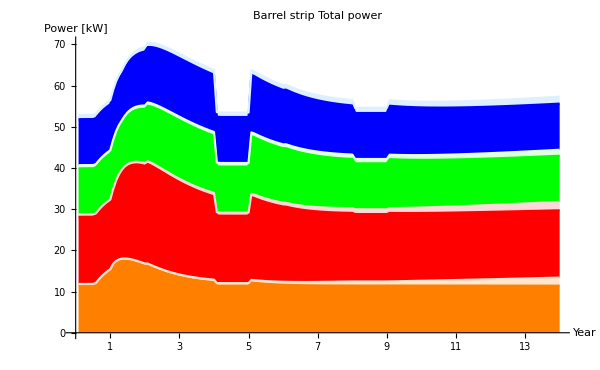

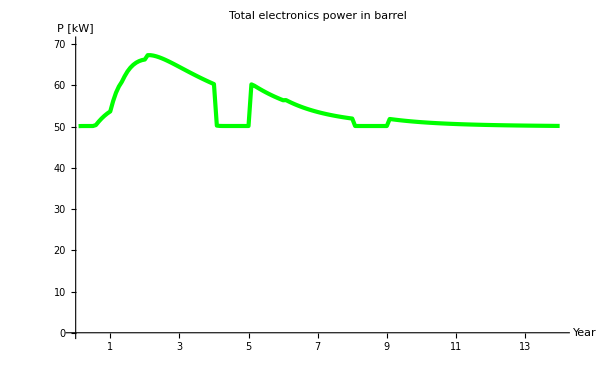

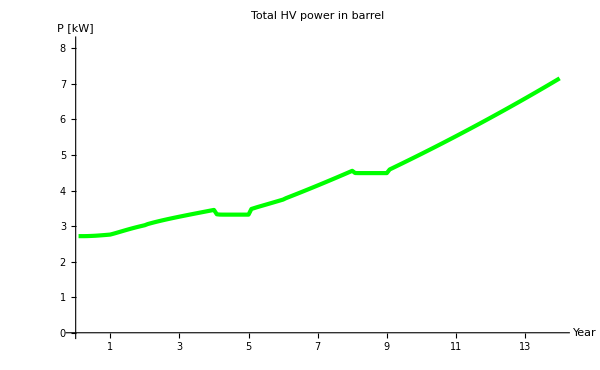

52.83

70.4008

133.259

```mathematica
power={pb1-phvb1,phvb1,pb2-phvb2,phvb2,pb3-phvb3,phvb3,pb3-phvb3,phvb4};
ListLinePlot[Accumulate[power],Filling->{1->{Axis,Orange},2->{{1},LightOrange},3->{{2},Red},4->{{3},LightRed},5->{{4},Green},6->{{5},LightGreen},7->{{6},Blue},8->{{7},LightBlue}},PlotStyle->{Orange,LightOrange,Red,LightRed,Green,LightGreen,Blue,LightBlue},AxesLabel->{"Year","Power [kW]"},PlotLabel->Style["Barrel strip Total power",Bold,24],Ticks->{ticklist,Automatic},AxesStyle->axesstyle,ImageSize->600]
totalelectronicspower = pb1-phvb1+pb2-phvb2+pb3-phvb3+pb3-phvb3;
totalhvpower = phvb1+phvb2+phvb3+phvb4;
ListLinePlot[totalelectronicspower ,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total electronics power in barrel",Bold,24],PlotRange->{{0,168},{0,Max[totalelectronicspower]+3}},plotformat]
ListLinePlot[totalhvpower ,AxesLabel->{"Year","P [kW]"},PlotLabel->Style["Total HV power in barrel",Bold,24],PlotRange->{{0,168},{0,Max[totalhvpower]+1}},plotformat]
Min[totalelectronicspower +totalhvpower ]
Max[totalelectronicspower +totalhvpower ]
100*Max[totalelectronicspower +totalhvpower ]/Min[totalelectronicspower +totalhvpower ]
```

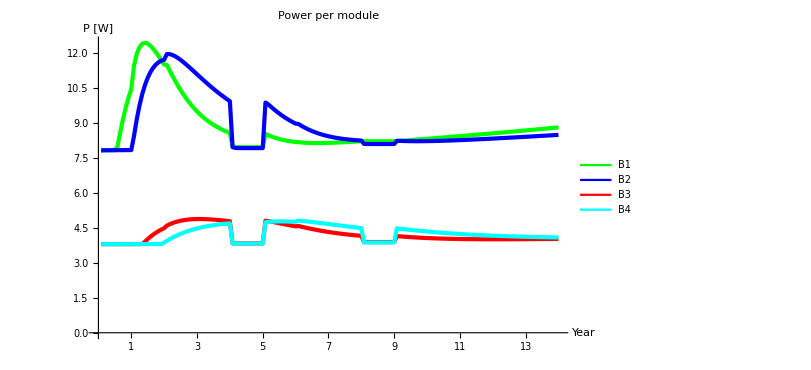

```mathematica
pmodb1plot=ListLinePlot[pmoduleb1,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{0,Automatic}},plotformat];
pmodb2plot=ListLinePlot[pmoduleb2,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{0,Automatic}},PlotStyle->{Blue,Thickness[0.005]},plotformat];
pmodb3plot=ListLinePlot[pmoduleb3,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{0,Automatic}},PlotStyle->{Red,Thickness[0.005]},plotformat];
pmodb4plot=ListLinePlot[pmoduleb4,AxesLabel->{"Year","P [W]"},PlotRange->{{0,168},{0,Automatic}},PlotStyle->{Cyan,Thickness[0.005]},plotformat];
Legended[Show[pmodb1plot,pmodb2plot,pmodb3plot,pmodb4plot,PlotLabel->"Power per module",LabelStyle->{Bold,24}],Placed[LineLegend[{Green,Blue,Red, Cyan},{ Style["B1",16,Bold],Style["B2",16,Bold],Style["B3",16,Bold],Style["B4",16,Bold]},LegendFunction->Framed],{{0.99,0.95},{1,1}}]]
```

```mathematica
Max[pmoduleb1]
Max[pmoduleb2]
Max[pmoduleb3]
Max[pmoduleb4]
Max[tfeastb1]
Max[itapeb1]
Max[tsb1[[1]],tsb1[[2]],tsb1[[3]],tsb1[[4]],tsb1[[5]],tsb1[[6]],tsb1[[7]],tsb1[[8]],tsb1[[9]],tsb1[[10]],tsb1[[11]],tsb1[[12]]]
Max[tsb1[[157]],tsb1[[158]],tsb1[[159]],tsb1[[160]],tsb1[[161]],tsb1[[162]],tsb1[[163]],tsb1[[164]],tsb1[[165]],tsb1[[166]],tsb1[[167]],tsb1[[168]]]
Max[tsb1]
Max[totalelectronicspower +totalhvpower ]
Max[totalhvpower ]
```

12.4523

11.9731

4.88445

4.81601

87.4528

0.978981

-17.6418

-19.7924

-14.9618

70.4008

7.15393

```mathematica
Max[pstaveb4]
```

132.895